# Neutrino induced Migdal events in xenon

This notebook calculates the rate of Migdal events due to nuclear recoils of low energy neutrinos in a xenon detector.

Gray (initialization) cells can/should be evaluated automatically
Blue cells create plots
Red cells are computations
Orange cells are input files
Purple cells create output files

## Constants

All units are in GeV unless otherwise explicitly noted

```mathematica
GeV=1;
MeV=10^-3 GeV;
keV=10^-6 GeV;
eV=10^-9 GeV;
ℏc=0.19732698;(*GeV fm*)
𝒸=2.997925 10^8;(*m/s*)
Gf=1.166 10^-5 1/GeV^2;
sin2Θw=0.2387;
(*particle masses*)
mn=0.93956542052; (*neutron mass*)
mp=0.93827; (*proton mass*)
amu=mn/1.00727; (*atomic mass unit*)
mπ=139.57MeV;(*pion mass*)
me=0.000511; (*electron mass*)
mμ=105.66MeV;(*muon mass*)

(*Useful units*)
Centimeter= 1/ℏc 10^13;
Second= 𝒸 10^2 Centimeter;
Kilogram=𝒸^2/(1.602 10^-19/eV);
KilogramDay= (1 Kilogram)(24 3600 Second);
cm2s=(Centimeter^2/(1(*cm^2*)))(Second/(1(*s*)));
μ[x_,y_]:=(x y)/(x+y)
```

```mathematica
(*Quark isospin and electric charge*)
I3u=1/2;
I3d=-1/2;
Qu = 2/3;
Qd = -1/3;
(*Renormalization*)
ρ=1.0086;
κ=0.9978;
λuL=-0.0031;
λuR=3.75 10^-5;
λdL=-0.0025;
λdR=7.5 10^-5;
(*Quark vector charges*)
qVu=ρ(I3u-2Qu κ sin2Θw)+λuL+λuR;
qVd=ρ(I3d -2Qd κ sin2Θw)+λdL+λdR;
(*Nucleon vector charges*)
qVp=2qVu+qVd;
qVn=qVu+2qVd;
```

Isotope data:

```mathematica
isotopesXe={{"xe128","xe129","xe130","xe131","xe132","xe134","xe136"},Table[54,7],{128,129,130,131,132,134,136},{.0191,.264,.0407,.212,.269,.1044,.0886}}//Thread;
isotopesAr={{"ar40",18,40,1}};
```

```mathematica
MtXe=131.293amu;
MtAr=39.95amu;
```

## Kinematics

### Neutrino

```mathematica
Enu^2+(Enu-Er-ΔE)^2-2Enu(Enu-Er-ΔE)(1-Cosθ)==mT^2+(mT+Er+ΔE)^2-2mT(mT+Er+ΔE)//FullSimplify
```

Cosθ Enu (Enu-Er-ΔE)==0

```mathematica
nuKin=2mT Er == Enu^2+(Enu-Er-ΔE)^2-2Enu (Enu-Er-ΔE)Cosθ//Solve[#,Er]&//FullSimplify
```

{{Er→Enu-Cosθ Enu+mT-√((-1+Cosθ^2) Enu^2-2 (-1+Cosθ) Enu mT+mT (mT-2 ΔE))-ΔE},{Er→Enu-Cosθ Enu+mT+√((-1+Cosθ^2) Enu^2-2 (-1+Cosθ) Enu mT+mT (mT-2 ΔE))-ΔE}}

```mathematica
With[{Enu=2MeV,mT=131amu,Cosθ=-1,ΔE=20keV},
Enu-Cosθ Enu+mT-√((-1+Cosθ^2) Enu^2-2 (-1+Cosθ) Enu mT+mT (mT-2 ΔE))-ΔE]
```

6.48141×10^-8

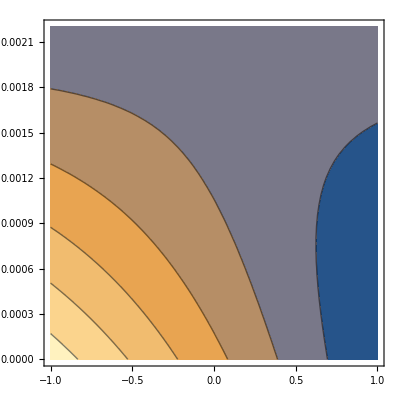

```mathematica
With[{Enu=2MeV,mT=131amu},
ContourPlot[Enu-Cosθ Enu+mT-√((-1+Cosθ^2) Enu^2-2 (-1+Cosθ) Enu mT+mT (mT-2 ΔE))-ΔE,{Cosθ,-1,1},{ΔE,0,2.2MeV},PlotRange->{0,All},ClippingStyle->None]]
```

```mathematica
2mT Er == Enu^2+(Enu-Er-ΔE)^2-2Enu (Enu-Er-ΔE)Cosθ//Solve[#,Er]&//FullSimplify
```

{{Er→Enu-Cosθ Enu+mT-√((-1+Cosθ^2) Enu^2-2 (-1+Cosθ) Enu mT+mT (mT-2 ΔE))-ΔE},{Er→Enu-Cosθ Enu+mT+√((-1+Cosθ^2) Enu^2-2 (-1+Cosθ) Enu mT+mT (mT-2 ΔE))-ΔE}}

Reproduce results (requires throwing away E_R^2 term, good approximation):

```mathematica
nuKin=((2mT Er == Enu^2+(Enu-Er-ΔE)^2-2Enu (Enu-Er-ΔE)Cosθ//Expand//Simplify//Series[#,{Er,0,1}]&//Normal)//Solve[#,Er]&//FullSimplify)
```

{{Er→-(-2 (-1+Cosθ) Enu^2+2 (-1+Cosθ) Enu ΔE+ΔE^2)/(2 ((-1+Cosθ) Enu-mT+ΔE))}}

```mathematica
eqERMAX=nuKin[[1,1]]/.Cosθ->-1//FullSimplify
```

Er→(-2 Enu+ΔE)^2/(2 (2 Enu+mT-ΔE))

```mathematica
nuKin[[1,1]]/.Cosθ->1//FullSimplify
```

Er→ΔE^2/(2 mT-2 ΔE)

```mathematica
nuKin=((2mT Er == Enu^2+(Enu-Er-ΔE)^2-2Enu (Enu-Er-ΔE)Cosθ//Expand//Simplify//Series[#,{Er,0,1}]&//Normal)//Solve[#,ΔE]&//FullSimplify)
```

{{ΔE→Enu-Cosθ Enu-Er-√((-1+Cosθ^2) Enu^2+Er (Er+2 mT))},{ΔE→Enu-Cosθ Enu-Er+√((-1+Cosθ^2) Enu^2+Er (Er+2 mT))}}

```mathematica
nuKin=((2mT Er == Enu^2+(Enu-Er-ΔE)^2-2Enu (Enu-Er-ΔE)Cosθ//Expand//Simplify//Series[#,{Er,0,1}]&//Normal)/.eqERMAX//Solve[#,ΔE]&//FullSimplify)
```

{{ΔE→Enu+mT-(√((1+Cosθ)^2 (Enu^2+mT^2)))/(1+Cosθ)},{ΔE→Enu+mT+(√((1+Cosθ)^2 (Enu^2+mT^2)))/(1+Cosθ)}}

```mathematica
Enu+mT-√(Enu^2+mT^2)
```

Enu+mT-√(Enu^2+mT^2)

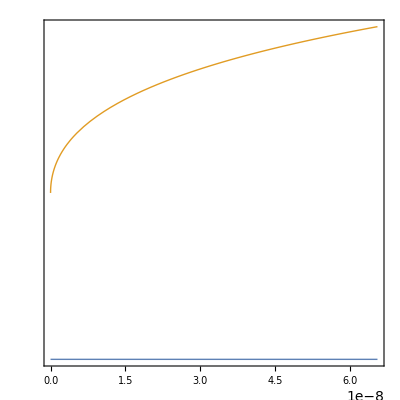

```mathematica
With[{Enu=2MeV,mT=131amu,Cosθ=-1},
LogPlot[{Enu+mT-√(Enu^2+mT^2),Enu-Cosθ Enu-Er+√((-1+Cosθ^2) Enu^2+Er (Er+2 mT))},{Er,0,(-2 Enu)^2/(2 (2 Enu+mT))}]]
```

```mathematica
nuKin=((2mT Er == Enu^2+(Enu-Er-ΔE)^2-2Enu (Enu-Er-ΔE)Cosθ)//Solve[#,ΔE]&//FullSimplify)
```

{{ΔE→Enu-Cosθ Enu-Er-√((-1+Cosθ^2) Enu^2+2 Er mT)},{ΔE→Enu-Cosθ Enu-Er+√((-1+Cosθ^2) Enu^2+2 Er mT)}}

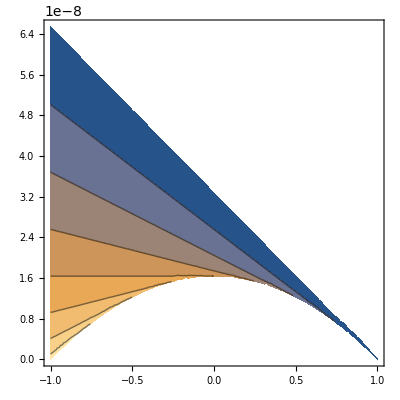

```mathematica
With[{Enu=2MeV,mT=131amu},
ContourPlot[Enu-Cosθ Enu-Er-√((-1+Cosθ^2) Enu^2+2 Er mT),{Cosθ,-1,1},{Er,0,(-2 Enu)^2/(2 (2 Enu+mT))},PlotRange->{0,All},ClippingStyle->None]]
```

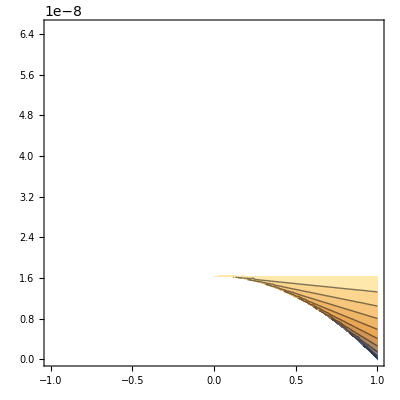

```mathematica
With[{Enu=2MeV,mT=131amu},
ContourPlot[Enu-Cosθ Enu-Er+√((-1+Cosθ^2) Enu^2+2 Er mT),{Cosθ,-1,1},{Er,0,(-2 Enu)^2/(2 (2 Enu+mT))},PlotRange->{0,2MeV},ClippingStyle->None]]
```

### Define functions

Bounds on recoil energy:

```mathematica
ErMin[Mt_?NumericQ,EM_?NumericQ]:=(2 EM^2)/(Mt-2EM)
ErMax[Mt_?NumericQ,Enu_?NumericQ,EM_?NumericQ]:=(2Enu-EM)^2/(2(Mt+2Enu))
```

```mathematica
EnuMin[Er_?NumericQ,Mt_?NumericQ,EM_?NumericQ]:=1/2 (Er+EM+√(Er^2+2 Er Mt +2 Er EM))
```

## Differential cross section

Use the Helm form factor

```mathematica
Fhelm[q_,A_]:=3(Sin[(q r)/ℏc]-((q r)/ℏc)Cos[(q r)/ℏc])/((q r)/ℏc)^3 Exp[(-((q s)/ℏc)^2)/2]/.{r->((1.23 A^(1/3)-.6)^2+7/3 π^2(0.52)^2-5(0.9)^2)^(1/2),s->0.9};
```

Differential cross section for coherent neutrino-nucleus scattering:

```mathematica
dσdEr[Er_,Enu_,iso_]:=(Gf^2(iso⟦3⟧ amu))/π(1-(iso⟦3⟧ amu Er)/(2 Enu^2 GeV))(iso⟦2⟧ qVp+(iso⟦3⟧-iso⟦2⟧) qVn)^2 Fhelm[√(2(iso⟦3⟧amu) Er),iso⟦3⟧]^2
```

## Neutrino fluxes

### Define sources

#### Reactor

Import normalized spectrum:

```mathematica
NotebookDirectory[]//SetDirectory;
reactorFlux=Import["data/reactor_flux.dat"]//{#[[All,1]]MeV,#[[All,2]]/MeV}&//Thread//Interpolation[#,InterpolationOrder->1]&;
eMaxR=reactorFlux[[1,1,2]];
```

Flux from a 1GW reactor at 10m:

```mathematica
rFluxNorm=(1.9 10^20)/(4π 1000^2)/cm2s;
```

#### SNS

Define spectra:

```mathematica
EνMbar=(mπ^2-mμ^2)/(2mπ);
eMaxSNS=mμ/2;
ΦSNSνE[Er_]=1/(29.7168 MeV)(3 (Er/(2/3 eMaxSNS))^2-2(Er/(2/3 eMaxSNS))^3)HeavisideTheta[eMaxSNS-Er];
ΦSNSνM[Er_]=1/(26.415 MeV)(3 (Er/eMaxSNS)^2-2(Er/eMaxSNS)^3)HeavisideTheta[eMaxSNS-Er];
```

SNS flux at 12m:

```mathematica
snsFluxNorm=(4.2 10^9/cm2s)/10^2;
```

Based on 8.5% neutrinos/proton on target and 1.4 MW beam:

```mathematica
(0.085 ν/proton)(1.4MW(10^6 Joule/s/MW))/(0.984 GeV/proton)1/(4π 100^2)
```

(0.96237 Joule ν)/s

#### Chromium source

A 60PBq C source at 1m (half life is ~30 days):

```mathematica
crFluxNorm= (60 10^15)/(4π 100)/cm2s;
```

4 lines, energies and branching ratios:

```mathematica
EνCr={745.8,750.7,425.7,430.6}keV;
BrCr={0.81,0.09,0.09,0.01};
```

```mathematica
EνCr1=745.8keV;BrCr1=0.81;
EνCr2=750.7keV;BrCr2=0.09;
EνCr3=425.7keV;BrCr3=0.09;
EνCr4=430.6keV;BrCr4=0.01;
```

#### pp solar neutrinos

Not used, but defined for comparison.

```mathematica
ppFlux=Import["data/pp_flux.dat"];
```

```mathematica
ppFlux[[All,1]]*=MeV;
```

```mathematica
ppFlux[[All,2]]/=MeV;
```

```mathematica
pp=ppFlux//Interpolation
```

InterpolatingFunction[…]

```mathematica
ppFluxNorm=5.98 10^10/cm2s;
```

### Flux plot

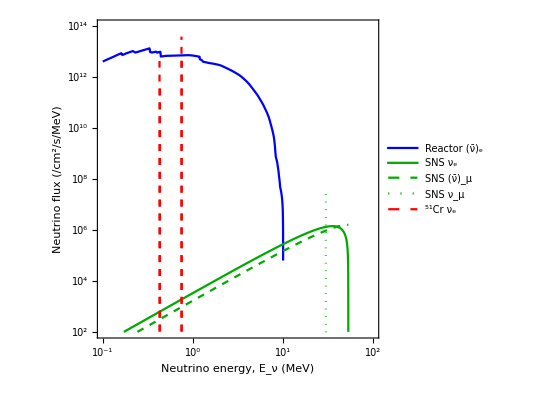

```mathematica
nuFluxPlot=Show[
LogLogPlot[{cm2s MeV rFluxNorm reactorFlux[er MeV],cm2s MeV snsFluxNorm ΦSNSνE[er MeV],cm2s MeV snsFluxNorm ΦSNSνM[er MeV]},{er,.1,100},
FrameLabel->{"Neutrino energy, E_ν (MeV)","Neutrino flux (/cm^2/s/MeV)"},
Epilog->Inset[Framed[Style[" "],RoundingRadius->4,FrameMargins->{{35,65},{55,55}}],Scaled[{.82,.78}]],
PlotLegends->Legend[{"Reactor (ν̄)_e","SNS ν_e","SNS (ν̄)_μ"},LegendMarkerSize->{20,10},Position->{.82,.85}],ImageSize->400,
PlotStyle->{Blue,Green//Darker,{Green//Darker,Dashed}},
FrameTicks->{LogTicks[10^1,10^14,2],LogTicks[10^-1,10^2]},
PlotRange->{{.1,100},{10^2,10^14}}],
ListLogLogPlot[{
{{0.999EνMbar/MeV,10^-100},{EνMbar/MeV,cm2s  snsFluxNorm}},
{{0.999EνCr⟦1⟧/MeV,10^-100},{EνCr⟦1⟧/MeV,cm2s  crFluxNorm BrCr⟦1⟧}},
{{0.999EνCr⟦2⟧/MeV,10^-100},{EνCr⟦2⟧/MeV,cm2s  crFluxNorm BrCr⟦2⟧}},
{{0.999EνCr⟦3⟧/MeV,10^-100},{EνCr⟦3⟧/MeV,cm2s  crFluxNorm BrCr⟦3⟧}},
{{0.999EνCr⟦4⟧/MeV,10^-100},{EνCr⟦4⟧/MeV,cm2s  crFluxNorm BrCr⟦4⟧}}},Joined->True,
PlotLegends->Legend[{"SNS ν_μ","^51Cr ν_e"},LegendMarkerSize->{20,10},Position->{.795,.665}],
PlotStyle->{{Green//Darker,Dotted},{Red,Dashed},{Red,Dashed},{Red,Dashed},{Red,Dashed}}]]
```

```mathematica
Export["figures/fig_nuFluxes.pdf",nuFluxPlot];
```

## Full elastic NR rate

### Define rates

Reactor:

```mathematica
dRrdExe[Er_?NumericQ,EM_?NumericQ]:=rFluxNorm/MtXe Sum[NIntegrate[ reactorFlux[Enu]isotopesXe[[ii,4]] dσdEr[Er,Enu,isotopesXe[[ii]]],{Enu,Min[EnuMin[Er,isotopesXe[[ii,3]]amu,EM],eMaxR],eMaxR},PrecisionGoal->3],{ii,Length[isotopesXe]}]
```

```mathematica
dRrdEar[Er_?NumericQ,EM_?NumericQ]:=rFluxNorm/MtAr NIntegrate[ reactorFlux[Enu]isotopesAr[[1,4]] dσdEr[Er,Enu,isotopesAr[[1]]],{Enu,Min[EnuMin[Er,isotopesAr[[1,3]]amu,EM],eMaxR],eMaxR},PrecisionGoal->3]
```

SNS:

```mathematica
dRsdExe[Er_?NumericQ,EM_?NumericQ]:=snsFluxNorm Sum[isotopesXe[[ii,4]]/(isotopesXe[[ii,3]]amu)(UnitStep[EνMbar-EnuMin[isotopesXe[[ii,3]] amu,Er,EM]]dσdEr[Er,EνMbar,isotopesXe[[ii]]]+NIntegrate[ (ΦSNSνE[Enu]+ΦSNSνM[Enu]) dσdEr[Er,Enu,isotopesXe[[ii]]],{Enu,Min[EnuMin[Er,isotopesXe[[ii,3]]amu,EM],eMaxSNS],eMaxSNS},PrecisionGoal->3]),{ii,Length[isotopesXe]}]
```

```mathematica
dRsdEar[Er_?NumericQ,EM_?NumericQ]:=snsFluxNorm isotopesAr[[1,4]]/(isotopesAr[[1,3]]amu)(UnitStep[EνMbar-EnuMin[isotopesAr[[1,3]] amu,Er,EM]]dσdEr[Er,EνMbar,isotopesAr[[1]]]+NIntegrate[ (ΦSNSνE[Enu]+ΦSNSνM[Enu]) dσdEr[Er,Enu,isotopesAr[[1]]],{Enu,Min[EnuMin[Er,isotopesAr[[1,3]]amu,EM],eMaxSNS],eMaxSNS},PrecisionGoal->3])
```

Chromium source:

```mathematica
dRcdExe[Er_?NumericQ,EM_?NumericQ]:= crFluxNorm Sum[isotopesXe[[ii,4]]/(isotopesXe[[ii,3]]amu)BrCr⟦jj⟧UnitStep[EνCr⟦jj⟧-EnuMin[Er,isotopesXe⟦ii,3⟧ amu,EM]]dσdEr[Er,EνCr⟦jj⟧,isotopesXe⟦ii⟧],{jj,Length[EνCr]},{ii,Length[isotopesXe]}]
```

```mathematica
dRcdEar[Er_?NumericQ,EM_?NumericQ]:= crFluxNorm 1/(isotopesAr[[1,3]]amu)Sum[BrCr⟦jj⟧UnitStep[EνCr⟦jj⟧-EnuMin[Er,isotopesAr⟦1,3⟧ amu,EM]]dσdEr[Er,EνCr⟦jj⟧,isotopesAr[[1]]],{jj,Length[EνCr]}]
```

### Calculate rates

Xenon rates:

```mathematica
XEreactorRateDat=ParallelTable[{er/keV,dRrdExe[er,0](KilogramDay keV  )},{er,logSpace[1eV,ErMax[128amu,eMaxR,0],200]}];
XEsnsRateDat=ParallelTable[{er/keV,dRsdExe[er,0](KilogramDay keV  )},{er,logSpace[1eV,ErMax[128amu,eMaxSNS,0],200]}];
XEcrRateDat=ParallelTable[{er/keV,dRcdExe[er,0](KilogramDay keV )},{er,logSpace[1eV,ErMax[128amu,EνCr//Max,0],200]}];
```

Argon rates:

```mathematica
ARreactorRateDat=ParallelTable[{er/keV,dRrdEar[er,0](KilogramDay keV  )},{er,logSpace[1eV,ErMax[40 amu/GeV,eMaxR,0],200]}];
ARsnsRateDat=ParallelTable[{er/keV,dRsdEar[er,0](KilogramDay keV  )},{er,logSpace[1eV,ErMax[40 amu/GeV,eMaxSNS,0],200]}];
ARcrRateDat=ParallelTable[{er/keV,dRcdEar[er,0](KilogramDay keV  )},{er,logSpace[1eV,ErMax[40 amu/GeV,EνCr//Max,0],200]}];
```

NIntegrate::zeroregion: Integration region {{0.05283,0.05283}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Enu near {Enu} = {0.05283}. NIntegrate obtained 7.76565×10^-26 and 1.61858×10^-27 for the integral and error estimates.

NIntegrate::zeroregion: Integration region {{0.05283,0.05283}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Enu near {Enu} = {0.05283}. NIntegrate obtained 1.55313×10^-25 and 3.23716×10^-27 for the integral and error estimates.

Export tabulated rate for thinNEST calculation (takes rate in units of /tonne/year/keV):

```mathematica
Export["results/snsNu_NR_xe.dat",{XEsnsRateDat[[All,1]],365250XEsnsRateDat[[All,2]]}//Thread];
Export["results/reactorNu_NR_xe.dat",{XEreactorRateDat[[All,1]],365250XEreactorRateDat[[All,2]]}//Thread];
Export["results/crNu_NR_xe.dat",{XEcrRateDat[[All,1]],365250XEcrRateDat[[All,2]]}//Thread];
```

#### Plot

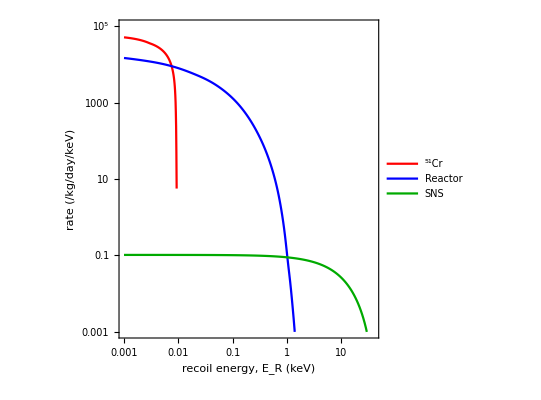
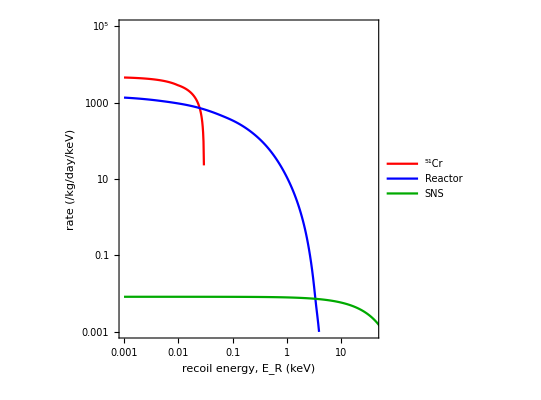

```mathematica
{ListLogLogPlot[{XEcrRateDat,XEreactorRateDat,XEsnsRateDat},Joined->True,
PlotStyle->{Red,Blue,Green//Darker},
PlotLegends->Legend[{"^51Cr","Reactor","SNS"}],
FrameLabel->{"recoil energy, E_R (keV)","rate (/kg/day/keV)"},
FrameTicks->{LogTicks[10^-4,10^6,2],LogTicks[10^-3,10^2]},
PlotRange->{{.001,40},{10^-3,10^5}}],
ListLogLogPlot[{ARcrRateDat,ARreactorRateDat,ARsnsRateDat},Joined->True,
PlotStyle->{Red,Blue,Green//Darker},
PlotLegends->Legend[{"^51Cr","Reactor","SNS"}],
FrameTicks->{LogTicks[10^-4,10^6,2],LogTicks[10^-3,10^2]},
FrameLabel->{"recoil energy, E_R (keV)","rate (/kg/day/keV)"},
PlotRange->{{.001,40},{10^-3,10^5}}]}
```

#### Integrated rate

```mathematica
XEreactorRateIntDat=ParallelTable[{ERmin/keV,NIntegrate[dRrdExe[er,0](KilogramDay),{er,ERmin,ErMax[128 amu/GeV,eMaxR,0]},PrecisionGoal->3]},    {ERmin,logSpace[1eV,ErMax[128 amu/GeV,eMaxR,0],100]}];
XEsnsRateIntDat=ParallelTable[{ERmin/keV,NIntegrate[dRsdExe[er,0](KilogramDay),         {er,ERmin,ErMax[128 amu/GeV,eMaxSNS,0]},PrecisionGoal->3]},{ERmin,logSpace[1eV,ErMax[128 amu/GeV,eMaxSNS,0],100]}];
XEcrRateIntDat=ParallelTable[{ERmin/keV,NIntegrate[dRcdExe[er,0](KilogramDay),           {er,ERmin,ErMax[128 amu/GeV,EνCr⟦1⟧,0]},PrecisionGoal->3]},{ERmin,logSpace[1eV,ErMax[128 amu/GeV,EνCr⟦1⟧,0],100]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
ARreactorRateIntDat=ParallelTable[{ERmin/keV,NIntegrate[dRrdEar[er,0](KilogramDay),{er,ERmin,ErMax[40 amu/GeV,eMaxR,0]},PrecisionGoal->3]},   {ERmin,logSpace[1eV,ErMax[40 amu/GeV,eMaxR,0],100]}];
ARsnsRateIntDat        =ParallelTable[{ERmin/keV,NIntegrate[dRsdEar[er,0](KilogramDay),{er,ERmin,ErMax[40 amu/GeV,eMaxSNS,0]},PrecisionGoal->3]},{ERmin,logSpace[1eV,ErMax[40 amu/GeV,eMaxSNS,0],100]}];
ARcrRateIntDat          =ParallelTable[{ERmin/keV,NIntegrate[dRcdEar[er,0](KilogramDay),{er,ERmin,ErMax[40 amu/GeV,EνCr⟦1⟧,0]},PrecisionGoal->3]},    {ERmin,logSpace[1eV,ErMax[40 amu/GeV,EνCr⟦1⟧,0],100]}];
```

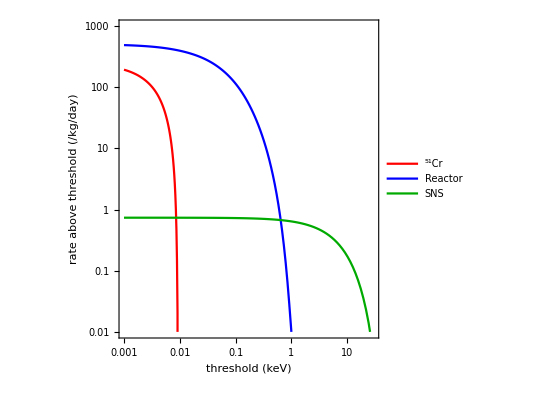
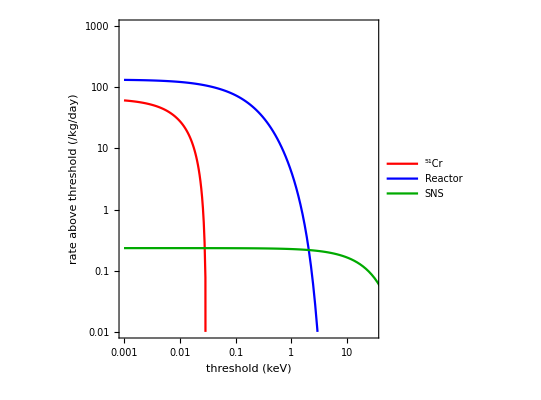

```mathematica
{ListLogLogPlot[{XEcrRateIntDat,XEreactorRateIntDat,XEsnsRateIntDat},Joined->True,
PlotStyle->{Red,Blue,Green//Darker},
PlotLegends->Legend[{"^51Cr","Reactor","SNS"}],
FrameLabel->{"threshold (keV)","rate above threshold (/kg/day)"},
FrameTicks->{LogTicks[10^-4,10^3],LogTicks[10^-3,10^2]},
PlotRange->{{.001,30},{.01,10^3}}],
ListLogLogPlot[{ARcrRateIntDat,ARreactorRateIntDat,ARsnsRateIntDat},Joined->True,
PlotStyle->{Red,Blue,Green//Darker},
PlotLegends->Legend[{"^51Cr","Reactor","SNS"}],
FrameLabel->{"threshold (keV)","rate above threshold (/kg/day)"},
FrameTicks->{LogTicks[10^-4,10^3],LogTicks[10^-3,10^2]},
PlotRange->{{.001,30},{.01,10^3}}]}
```

## Migdal rate

### Import

```mathematica
datXe=Import["data/Xe_new.dat"];
datSepXe=Table[datXe[[4+254j;;254+254j]],{j,0,Floor[Length[datXe]/256]}];
```

```mathematica
datAr=Import["data/Ar.dat"];
datSepAr=Table[datAr[[4+254j;;254+254j]],{j,0,Floor[Length[datAr]/256]}];
```

#### Reproducing Fig.3 of Ibe et al.

Xenon

```mathematica
datN1=Table[datXe[[4+254j;;254+254j]],{j,0,0}];
datN2=Table[datXe[[4+254j;;254+254j]],{j,1,2}];
datN3=Table[datXe[[4+254j;;254+254j]],{j,3,5}];
datN4=Table[datXe[[4+254j;;254+254j]],{j,6,8}];
datN5=Table[datXe[[4+254j;;254+254j]],{j,9,10}];
```

```mathematica
totN1={datN1[[1,All,1]]/1000,1000/(2π)((10^-3 me)/(10^-9(*1eV*)))^2 datN1[[All,All,2]][[1]]}//Thread;
totN2={datN2[[1,All,1]]/1000,1000/(2π)((10^-3 me)/(10^-9(*1eV*)))^2 Apply[Plus,datN2[[All,All,2]]]}//Thread;
totN3={datN3[[1,All,1]]/1000,1000/(2π)((10^-3 me)/(10^-9(*1eV*)))^2 Apply[Plus,datN3[[All,All,2]]]}//Thread;
totN4={datN4[[1,All,1]]/1000,1000/(2π)((10^-3 me)/(10^-9(*1eV*)))^2 Apply[Plus,datN4[[All,All,2]]]}//Thread;
totN5={datN5[[1,All,1]]/1000,1000/(2π)((10^-3 me)/(10^-9(*1eV*)))^2 Apply[Plus,datN5[[All,All,2]]]}//Thread;
```

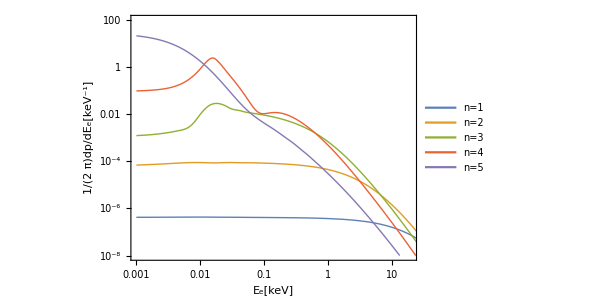

```mathematica
plot=ListLogLogPlot[{totN1,totN2,totN3,totN4,totN5},Joined->True,AspectRatio->.7,PlotRange->{{.001,20},{10^-8,100}},PlotLegends->Legend[{"n=1","n=2","n=3","n=4","n=5"}],FrameLabel->{"E_e[keV]","1/(2  π)dp/dE_e[keV^-1]"},FrameTicks->{LogTicks[10^-8,100,2],LogTicks[.001,10]}]
```

### Definitions

Momentum transfer to electron:

```mathematica
qe[Er_,Mt_]=me √((2Er)/Mt);
```

List of states contained in the file

```mathematica
statesXe=Table[datXe[[2+254j]],{j,0,Floor[Length[datXe]/256]}];
statesAr=Table[datAr[[2+254j]],{j,0,Floor[Length[datAr]/256]}];
```

List of binding energies of the states in keV

```mathematica
EstatesXe=eV{3.5 10^4,5.4 10^3,4.9 10^3,1.1 10^3,9.3 10^2,6.6 10^2,2.0 10^2,1.4 10^2,6.1 10,2.1 10,9.8};
EstatesAr=eV{3.2  10^3,3.0 10^2,2.4 10^2,2.7 10,1.3 10};
```

Array of binding energies, can be accessed as Enl[[n,l]]

```mathematica
EnlXe=eV{{3.5 10^4,0,0,0},{5.4 10^3,4.9 10^3,0,0},{1.1 10^3,9.3 10^3,6.6 10^2,0},{2.0 10^2,1.4 10^2,6.1 10,0.85},{2.1 10,9.8,1.6,0},{6.3,2.2,0,0}};
EnlAr=eV{{3.2 10^3,0,0,0},{3.2 10^2,2.4 10^2,0,0},{2.7 10,13,0,0},{0,0,0,0}};
```

Ionization probability for the n,l state into a free state with momentum qe and kinetic energy Ee

```mathematica
z[x_]=0;
znlxeTable=Table[If[EnlXe[[ni,li+1]]>0,(Switch@@Join[{{ni,li}},({statesXe,Table[datSepXe[[i]]//Interpolation,{i,1,datSepXe//Length}]}//Thread//Flatten[#,1]&)]),z],{ni,1,Length[EnlXe]},{li,0,3}];
```

```mathematica
ZnlXe[n_?IntegerQ,l_?IntegerQ,qe_?NumericQ,Ee_?NumericQ]:=(qe/(10^-9(*1eV in GeV*)))^2 10^9/(2π)If[Ee<10^-9,
znlxeTable⟦n,l+1⟧[1],
If[Ee>70 10^-6,
0,
znlxeTable⟦n,l+1⟧[Ee 10^9]]
];
```

```mathematica
znlArTable=Table[If[EnlAr[[ni,li+1]]>0,(Switch@@Join[{{ni,li}},({statesAr,Table[datSepAr[[i]]//Interpolation,{i,1,datSepAr//Length}]}//Thread//Flatten[#,1]&)]),z],{ni,1,Length[EnlAr]},{li,0,3}];
```

```mathematica
ZnlAr[n_?IntegerQ,l_?IntegerQ,qe_?NumericQ,Ee_?NumericQ]:=(qe/(10^-9(*1eV in GeV*)))^2 10^9/(2π)If[Ee<10^-9,
znlArTable⟦n,l+1⟧[1],
If[Ee>70 10^-6,
0,
znlArTable⟦n,l+1⟧[Ee 10^9]]
];
```

Calc total probability at qe = 1eV

```mathematica
totMigProbXe=Table[NIntegrate[ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],10^-9,ee],{ee,10^-9,70 10^-6}],{nl,1,Length[EstatesXe]}];
totMigProbAr=Table[NIntegrate[ZnlAr[statesAr[[nl,1]],statesAr[[nl,2]],10^-9,ee],{ee,10^-9,70 10^-6}],{nl,1,Length[EstatesAr]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {3.62073×10^-8}. NIntegrate obtained 1.36735×10^-8 and 1.85507×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {4.10041×10^-7}. NIntegrate obtained 1.35932×10^-9 and 2.67507×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {2.06593×10^-8}. NIntegrate obtained 1.38585×10^-7 and 5.67367×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {2.06593×10^-8}. NIntegrate obtained 1.75068×10^-8 and 2.82658×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {1.23685×10^-7}. NIntegrate obtained 5.21101×10^-9 and 3.75634×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {1.06431×10^-8}. NIntegrate obtained 2.43955×10^-7 and 7.56801×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
totalMigProbNLxe[nl_,qe_]:=(qe/10^-9)^2 totMigProbXe[[nl]]
totalMigProbNLar[nl_,qe_]:=(qe/10^-9)^2 totMigProbAr[[nl]]
```

This should match table II of Ibe et al.:

```mathematica
Table[totalMigProbNLxe[nl,me 10^-3],{nl,1,Length[EstatesXe]}]//NumberForm[#,2]&
```

{4.9×10^-6,0.00003,0.00013,0.00011,0.0006,0.0036,0.00035,0.0015,0.036,0.00047,0.078}

```mathematica
Table[totalMigProbNLar[nl,me 10^-3],{nl,1,Length[EstatesAr]}]//NumberForm[#,2]&
```

{0.000073,0.00053,0.0046,0.0014,0.064}

Lindhard factors:

```mathematica
LXe=0.15;
LAr=0.25;
```

### Differential rate

#### Define rate for individual levels

Xenon:

```mathematica
dRmigdEdetNsnsXe[Edet_?NumericQ,Ni_?IntegerQ]:= NIntegrate[dRsdExe[Er,Edet-Er LXe]*
 Sum[
UnitStep[Edet-Er LXe -EstatesXe[[nl]]]*
ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],qe[Er,131 amu],Edet-Er LXe -EstatesXe[[nl]]],
{nl,Position[statesXe[[All,1]],Ni]//Flatten}],
{Er,ErMin[128amu,Edet],ErMax[128amu,eMaxSNS,0]},PrecisionGoal->3,AccuracyGoal->Infinity]
```

```mathematica
dRmigdEdetNreactorXe[Edet_?NumericQ,Ni_?IntegerQ]:= NIntegrate[dRrdExe[Er,Edet-Er LXe]*
 Sum[
UnitStep[Edet-Er LXe -EstatesXe[[nl]]]*
ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],qe[Er,131 amu],Edet-Er LXe -EstatesXe[[nl]]],
{nl,Position[statesXe[[All,1]],Ni]//Flatten}],
{Er,ErMin[128amu,Edet],ErMax[128amu,eMaxR,0]},PrecisionGoal->3,AccuracyGoal->Infinity]
```

```mathematica
dRmigdEdetNcrXe[Edet_?NumericQ,Ni_?IntegerQ]:= NIntegrate[dRcdExe[Er,Edet-Er LXe]*
 Sum[
UnitStep[Edet-Er LXe -EstatesXe[[nl]]]*
ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],qe[Er,131 amu],Edet-Er LXe -EstatesXe[[nl]]],
{nl,Position[statesXe[[All,1]],Ni]//Flatten}],
{Er,ErMin[128amu,Edet],ErMax[128amu,EνCr1,0]},PrecisionGoal->2]
```

Argon:

```mathematica
dRmigdEdetNsnsAr[Edet_?NumericQ,Ni_?IntegerQ]:= NIntegrate[dRsdEar[Er,Edet-Er LAr]*
 Sum[
UnitStep[Edet-Er LAr -EstatesAr[[nl]]]*
ZnlAr[statesAr[[nl,1]],statesAr[[nl,2]],qe[Er,40 amu],Edet-Er LAr -EstatesAr[[nl]]],
{nl,Position[statesAr[[All,1]],Ni]//Flatten}],
{Er,0,ErMax[40amu,eMaxSNS,0]},PrecisionGoal->2]
```

```mathematica
dRmigdEdetNreactorAr[Edet_?NumericQ,Ni_?IntegerQ]:= NIntegrate[dRrdExe[Er,Edet-Er LXe]*
  Sum[
UnitStep[Edet-Er LAr -EstatesAr[[nl]]]*
ZnlAr[statesAr[[nl,1]],statesAr[[nl,2]],qe[Er,40 amu],Edet-Er LAr -EstatesAr[[nl]]],
{nl,Position[statesAr[[All,1]],Ni]//Flatten}],
{Er,0,ErMax[40amu,eMaxR,0]},PrecisionGoal->2]
```

```mathematica
dRmigdEdetNcrAr[Edet_?NumericQ,Ni_?IntegerQ]:= NIntegrate[dRcdExe[Er,Edet-Er LXe]*
 Sum[
UnitStep[Edet-Er LAr -EstatesAr[[nl]]]*
ZnlAr[statesAr[[nl,1]],statesAr[[nl,2]],qe[Er,40 amu],Edet-Er LAr -EstatesAr[[nl]]],
{nl,Position[statesAr[[All,1]],Ni]//Flatten}],
{Er,0,ErMax[40amu,EνCr1,0]},PrecisionGoal->2]
```

#### Approximate rate

This version of the rate calculation ignores the effect of different isotopes, which is a reasonable approximation.

```mathematica
MtXe=131.3amu;
MtAr=40amu;
```

Xenon:

```mathematica
dRmigdEdetNreactorXe[Edet_?NumericQ,Ni_?IntegerQ]:= rFluxNorm/MtXe NIntegrate[
reactorFlux[Enu] dσdEr[Er,Enu,isotopesXe[[4]]]*
 Sum[
UnitStep[Edet-Er LXe -EstatesXe[[nl]]]*
ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],qe[Er,131 amu],Edet-Er LXe -EstatesXe[[nl]]],
{nl,Position[statesXe[[All,1]],Ni]//Flatten}],
{Er,ErMin[128amu,Edet],Min[ErMax[128amu,eMaxR,0],Edet/LXe]},
{Enu,Min[EnuMin[Er,isotopesXe[[1,3]]amu,Edet-Er LXe],eMaxR],eMaxR},PrecisionGoal->3,AccuracyGoal->30]
```

```mathematica
dRmigdEdetNsnsXe[Edet_?NumericQ,Ni_?IntegerQ]:= snsFluxNorm/MtXe NIntegrate[
(UnitStep[EνMbar-EnuMin[isotopesXe[[1,3]] amu,Er,Edet-Er LXe]]dσdEr[Er,EνMbar,isotopesXe[[4]]]+(ΦSNSνE[Enu]+ΦSNSνM[Enu])dσdEr[Er,Enu,isotopesXe[[4]]])
 Sum[
UnitStep[Edet-Er LXe -EstatesXe[[nl]]]*
ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],qe[Er,131 amu],Edet-Er LXe -EstatesXe[[nl]]],
{nl,Position[statesXe[[All,1]],Ni]//Flatten}],
{Er,ErMin[128amu,Edet],Min[ErMax[128amu,eMaxSNS,0],Edet/LXe]},
{Enu,Min[EnuMin[Er,isotopesXe[[1,3]]amu,Edet-Er LXe],eMaxSNS],eMaxSNS},PrecisionGoal->3,AccuracyGoal->30,MinRecursion->4]
```

```mathematica
dRmigdEdetNcrXe[Edet_?NumericQ,Ni_?IntegerQ]:= crFluxNorm/MtXe NIntegrate[
Sum[BrCr⟦jj⟧UnitStep[EνCr⟦jj⟧,EnuMin[Er,isotopesXe⟦1,3⟧ amu,Edet-Er LXe]]dσdEr[Er,EνCr⟦jj⟧,isotopesXe⟦4⟧],{jj,Length[EνCr]}]
 Sum[
UnitStep[Edet-Er LXe -EstatesXe[[nl]]]*
ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],qe[Er,131 amu],Edet-Er LXe -EstatesXe[[nl]]],
{nl,Position[statesXe[[All,1]],Ni]//Flatten}],
{Er,ErMin[128amu,Edet],ErMax[128amu,EνCr1,0]},PrecisionGoal->3,AccuracyGoal->30]
```

Argon:

```mathematica
dRmigdEdetNreactorAr[Edet_?NumericQ,Ni_?IntegerQ]:= rFluxNorm/MtAr NIntegrate[
reactorFlux[Enu] dσdEr[Er,Enu,isotopesAr[[1]]]*
  Sum[
UnitStep[Edet-Er LAr -EstatesAr[[nl]]]*
ZnlAr[statesAr[[nl,1]],statesAr[[nl,2]],qe[Er,40 amu],Edet-Er LAr -EstatesAr[[nl]]],
{nl,Position[statesAr[[All,1]],Ni]//Flatten}],
{Er,ErMin[40amu,Edet],Min[ErMax[40amu,eMaxR,0],Edet/LXe]},
{Enu,Min[EnuMin[Er,isotopesAr[[1,3]]amu,Edet-Er LAr],eMaxR],eMaxR},PrecisionGoal->3,AccuracyGoal->30]
```

```mathematica
dRmigdEdetNsnsAr[Edet_?NumericQ,Ni_?IntegerQ]:= snsFluxNorm/MtAr NIntegrate[
(UnitStep[EνMbar-EnuMin[isotopesAr[[1,3]] amu,Er,Edet-Er LAr]]dσdEr[Er,EνMbar,isotopesAr[[1]]]+(ΦSNSνE[Enu]+ΦSNSνM[Enu])dσdEr[Er,Enu,isotopesAr[[1]]])*
 Sum[
UnitStep[Edet-Er LAr -EstatesAr[[nl]]]*
ZnlAr[statesAr[[nl,1]],statesAr[[nl,2]],qe[Er,40 amu],Edet-Er LAr -EstatesAr[[nl]]],
{nl,Position[statesAr[[All,1]],Ni]//Flatten}],
{Er,ErMin[40amu,Edet],Min[ErMax[40amu,eMaxSNS,0],Edet/LXe]},
{Enu,Min[EnuMin[Er,isotopesAr[[1,3]]amu,Edet-Er LAr],eMaxSNS],eMaxSNS},PrecisionGoal->3,AccuracyGoal->30,MinRecursion->4]
```

```mathematica
dRmigdEdetNcrAr[Edet_?NumericQ,Ni_?IntegerQ]:=crFluxNorm/MtAr NIntegrate[
Sum[BrCr⟦jj⟧UnitStep[EνCr⟦jj⟧-EnuMin[Er,isotopesAr⟦1,3⟧ amu,Edet-Er LAr]]dσdEr[Er,EνCr⟦jj⟧,isotopesAr⟦1⟧],{jj,Length[EνCr]}]
 Sum[
UnitStep[Edet-Er LAr -EstatesAr[[nl]]]*
ZnlAr[statesAr[[nl,1]],statesAr[[nl,2]],qe[Er,40 amu],Edet-Er LAr -EstatesAr[[nl]]],
{nl,Position[statesAr[[All,1]],Ni]//Flatten}],
{Er,ErMin[40amu,Edet],ErMax[40amu,EνCr//Max,0]},PrecisionGoal->3,AccuracyGoal->30]
```

#### calculate rates

Xenon:

```mathematica
XEdataEM3r=ParallelTable[{Em/keV,dRmigdEdetNreactorXe[Em,3](KilogramDay keV)},{Em,logSpace[EnlXe[[3,3]],6keV,100]}];
XEdataEM4r=ParallelTable[{Em/keV,dRmigdEdetNreactorXe[Em,4](KilogramDay keV)},{Em,logSpace[EnlXe[[4,3]],4keV,100]}];
XEdataEM5r=ParallelTable[{Em/keV,dRmigdEdetNreactorXe[Em,5](KilogramDay keV)},{Em,logSpace[EnlXe[[5,2]],2keV,100]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
XEdataEM3s=ParallelTable[{Em/keV,dRmigdEdetNsnsXe[Em,3](KilogramDay keV)},{Em,logSpace[EnlXe[[3,3]],8keV,100]}];
XEdataEM4s=ParallelTable[{Em/keV,dRmigdEdetNsnsXe[Em,4](KilogramDay keV)},{Em,logSpace[EnlXe[[4,3]],7keV,100]}];
XEdataEM5s=ParallelTable[{Em/keV,dRmigdEdetNsnsXe[Em,5](KilogramDay keV)},{Em,logSpace[EnlXe[[5,2]],7keV,150]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
XEdataEM3c=ParallelTable[{Em/keV,dRmigdEdetNcrXe[Em,3](KilogramDay keV)},{Em,logSpace[EnlXe[[3,3]],6keV,100]}];
XEdataEM4c=ParallelTable[{Em/keV,dRmigdEdetNcrXe[Em,4](KilogramDay keV)},{Em,logSpace[EnlXe[[4,3]],4keV,100]}];
XEdataEM5c=ParallelTable[{Em/keV,dRmigdEdetNcrXe[Em,5](KilogramDay keV)},{Em,logSpace[EnlXe[[5,2]],2keV,200]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {1.7832×10^-9}. NIntegrate obtained 3.66881×10^-12 and 4.44452×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Argon:

```mathematica
ARdataEM3r=ParallelTable[{Em/keV,dRmigdEdetNreactorAr[Em,3](KilogramDay keV)},{Em,logSpace[EnlAr[[3,2]],6keV,100]}];
ARdataEM2r=ParallelTable[{Em/keV,dRmigdEdetNreactorAr[Em,2](KilogramDay keV)},{Em,logSpace[EnlAr[[2,2]],8keV,100]}];
ARdataEM1r=ParallelTable[{Em/keV,dRmigdEdetNreactorAr[Em,1](KilogramDay keV)},{Em,logSpace[EnlAr[[1,1]],11keV,100]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in Er near {Er,Enu} = {0.578868,0.422062}. NIntegrate obtained 1.20006×10^-11 and 1.26985×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in Er near {Er,Enu} = {0.582454,0.422062}. NIntegrate obtained 6.69904×10^-12 and 1.20981×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in Er near {Er,Enu} = {0.584499,0.422062}. NIntegrate obtained 4.01461×10^-12 and 7.33536×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in Er near {Er,Enu} = {0.589313,0.211031}. NIntegrate obtained 4.41931×10^-13 and 5.61131×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in Er near {Er,Enu} = {0.733024,0.422062}. NIntegrate obtained 3.03862×10^-14 and 5.89377×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in Er near {Er,Enu} = {0.589954,0.211031}. NIntegrate obtained 2.57744×10^-13 and 3.95365×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in Er near {Er,Enu} = {0.607028,0.461031}. NIntegrate obtained 1.43132×10^-13 and 1.72889×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
ARdataEM3s=ParallelTable[{Em/keV,dRmigdEdetNsnsAr[Em,3](KilogramDay keV)},{Em,logSpace[EnlAr[[3,2]],40keV,100]}];
ARdataEM2s=ParallelTable[{Em/keV,dRmigdEdetNsnsAr[Em,2](KilogramDay keV)},{Em,logSpace[EnlAr[[2,2]],40keV,100]}];
ARdataEM1s=ParallelTable[{Em/keV,dRmigdEdetNsnsAr[Em,1]( KilogramDay keV)},{Em,logSpace[EnlAr[[1,1]],40keV,100]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
ARdataEM3c=ParallelTable[{Em/keV,dRmigdEdetNcrAr[Em,3](KilogramDay keV)},{Em,logSpace[EnlAr[[3,2]],2keV,100]}];
ARdataEM2c=ParallelTable[{Em/keV,dRmigdEdetNcrAr[Em,2](KilogramDay keV)},{Em,logSpace[EnlAr[[2,2]],3keV,100]}];
ARdataEM1c=ParallelTable[{Em/keV,dRmigdEdetNcrAr[Em,1](KilogramDay keV)},{Em,logSpace[EnlAr[[1,1]],6keV,100]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {5.6043×10^-9}. NIntegrate obtained 1.52725×10^-12 and 2.11574×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Transform NR energies:

```mathematica
XEreactorRateEdetDat=XEreactorRateDat;
XEreactorRateEdetDat[[All,1]]*=LXe;
XEreactorRateEdetDat[[All,2]]/=LXe ;
XEsnsRateEdetDat=XEsnsRateDat;
XEsnsRateEdetDat[[All,1]]*=LXe;
XEsnsRateEdetDat[[All,2]]/=LXe ;
XEcrRateEdetDat= XEcrRateDat;
XEcrRateEdetDat[[All,1]]*=LXe;
XEcrRateEdetDat[[All,2]]/=LXe;
```

```mathematica
ARreactorRateEdetDat=ARreactorRateDat;
ARreactorRateEdetDat[[All,1]]*=LAr;
ARreactorRateEdetDat[[All,2]]/=LAr ;
ARsnsRateEdetDat=ARsnsRateDat;
ARsnsRateEdetDat[[All,1]]*=LAr;
ARsnsRateEdetDat[[All,2]]/=LAr ;
ARcrRateEdetDat= ARcrRateDat;
ARcrRateEdetDat[[All,1]]*=LAr;
ARcrRateEdetDat[[All,2]]/=LAr ;
```

#### Plots

```mathematica
optXe={PlotStyle->{Black,Green,Blue,Red},Filling->Bottom,
FrameTicks->{LogTicks[10^-7,10^10,2],LogTicks[10^-6,10^2]},
FrameLabel->{"Detected energy, E_det (keV_ee)","Differential rate (/keV_ee/kg/day)"},
PlotLegends->Legend[{"NR","n = 3","n = 4","n = 5"},Position->{.86,.82},LegendFunction->(Framed[#,RoundingRadius->5]&)],
Epilog->Inset[Framed[Style["xenon",18,FontFamily->"Times"],RoundingRadius->5,Background->White],Scaled[{.12,.08}]]};

optAr={PlotStyle->{Black,Green,Blue,Red},Filling->Bottom,
FrameTicks->{LogTicks[10^-7,10^10,2],LogTicks[10^-3,10^2]},
FrameLabel->{"Detected energy, E_det(keV_ee)","Differential rate (/keV_ee/kg/day)"},
PlotLegends->Legend[{"NR","n = 3","n = 4","n = 5"},Position->{.86,.82},LegendFunction->(Framed[#,RoundingRadius->5]&)],
Epilog->Inset[Framed[Style["argon",18,FontFamily->"Times"],RoundingRadius->5,Background->White],Scaled[{.12,.08}]]};
```

Reactor:

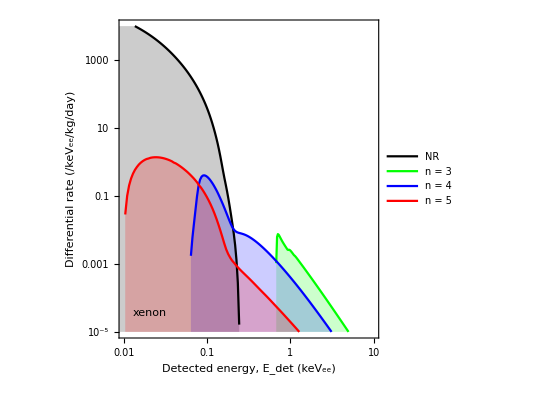
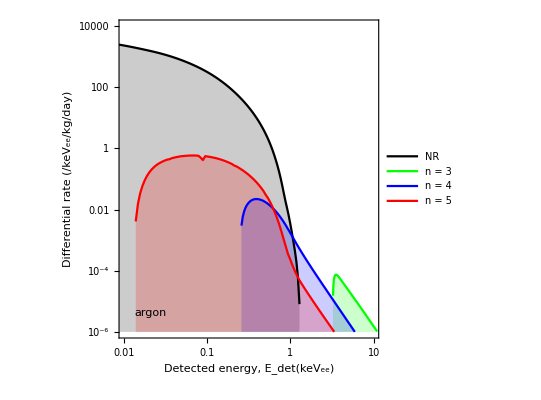

```mathematica
{XEmigPlotR=ListLogLogPlot[{XEreactorRateEdetDat,XEdataEM3r,XEdataEM4r,XEdataEM5r},Joined->True,
PlotRange->{{.01,10},{10^-5,10^4}},optXe],
ARmigPlotR=ListLogLogPlot[{ARreactorRateEdetDat,ARdataEM1r,ARdataEM2r,ARdataEM3r},Joined->True,
PlotRange->{{.01,10},{10^-6,10^4}},optAr]}
```

SNS:

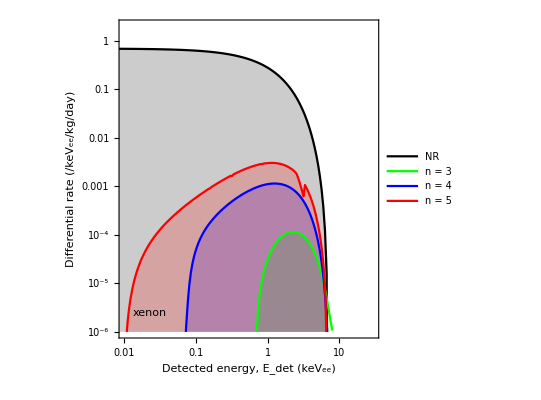
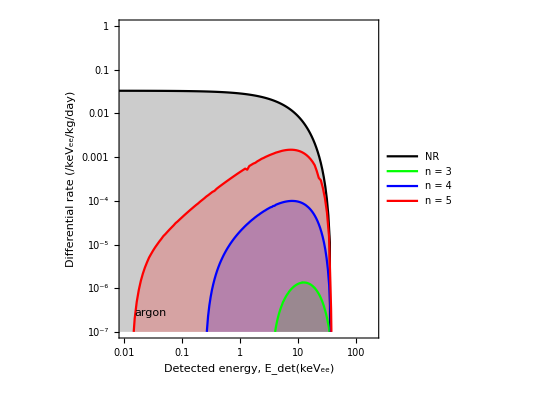

```mathematica
{XEmigPlotS=ListLogLogPlot[{XEsnsRateEdetDat, XEdataEM3s,XEdataEM4s,XEdataEM5s},Joined->True,
PlotRange->{{.01,30},{10^-6,2 10^0}},optXe],
ARmigPlotS=ListLogLogPlot[{ARsnsRateEdetDat, ARdataEM1s,ARdataEM2s,ARdataEM3s},Joined->True,
PlotRange->{{.01,200},{10^-7,10^0}},optAr]}
```

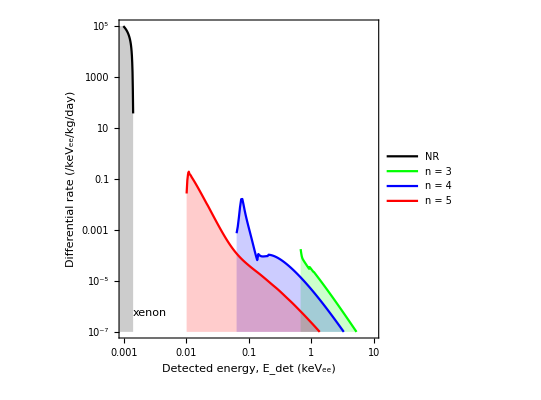
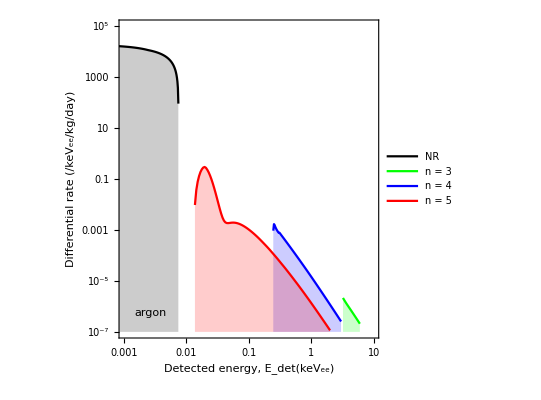

```mathematica
{XEmigPlotCr=ListLogLogPlot[{XEcrRateEdetDat,XEdataEM3c,XEdataEM4c,XEdataEM5c},Joined->True,
PlotRange->{{.001,10},{10^-7,10^5}},optXe],
ARmigPlotCr=ListLogLogPlot[{ARcrRateEdetDat,ARdataEM1c,ARdataEM2c,ARdataEM3c},Joined->True,
PlotRange->{{.001,10},{10^-7,10^5}},optAr]}
```

```mathematica
Export["figures/fig_xe_reactorNu_rates.pdf",XEmigPlotR];
Export["figures/fig_xe_snsNu_rates.pdf",XEmigPlotS];
Export["figures/fig_xe_crNu_rates.pdf",XEmigPlotCr];
Export["figures/fig_ar_reactorNu_rates.pdf",ARmigPlotR];
Export["figures/fig_ar_snsNu_rates.pdf",ARmigPlotS];
Export["figures/fig_ar_crNu_rates.pdf",ARmigPlotCr];
```

### Combined rate plots

Create interpolation functions from previous rate data:

Xenon:

```mathematica
XEmig3r=XEdataEM3r//Interpolation;
XEmig4r=XEdataEM4r//Interpolation;
XEmig5r=XEdataEM5r//Interpolation;
XEmigRateReactor[er_]=XEmig3r[er]UnitStep[er-XEdataEM3r[[1,1]]]UnitStep[XEdataEM3r[[-1,1]]-er]+XEmig4r[er]UnitStep[er-XEdataEM4r[[1,1]]]UnitStep[XEdataEM4r[[-1,1]]-er]+XEmig5r[er]UnitStep[er-XEdataEM5r[[1,1]]]UnitStep[XEdataEM5r[[-1,1]]-er];
```

```mathematica
XEmig3sns=XEdataEM3s//Interpolation;
XEmig4sns=XEdataEM4s//Interpolation;
XEmig5sns=XEdataEM5s//Interpolation;
XEmigRateSNS[er_]=XEmig3sns[er]UnitStep[er-XEdataEM3s[[1,1]]]UnitStep[XEdataEM3s[[-1,1]]-er]+XEmig4sns[er]UnitStep[er-XEdataEM4s[[1,1]]]UnitStep[XEdataEM4s[[-1,1]]-er]+XEmig5sns[er]UnitStep[er-XEdataEM5s[[1,1]]]UnitStep[XEdataEM5s[[-1,1]]-er];
```

```mathematica
XEmig3cr=XEdataEM3c//Interpolation;
XEmig4cr=XEdataEM4c//Interpolation;
XEmig5cr=XEdataEM5c//Interpolation;
XEmigRateCr[er_]=XEmig3cr[er]UnitStep[er-XEdataEM3c[[1,1]]]UnitStep[XEdataEM3c[[-1,1]]-er]+XEmig4cr[er]UnitStep[er-XEdataEM4c[[1,1]]]UnitStep[XEdataEM4c[[-1,1]]-er]+XEmig5cr[er]UnitStep[er-XEdataEM5c[[1,1]]]UnitStep[XEdataEM5c[[-1,1]]-er];
```

Argon:

```mathematica
ARmig1r=ARdataEM1r//Interpolation;
ARmig2r=ARdataEM2r//Interpolation;
ARmig3r=ARdataEM3r//Interpolation;
ARmigRateReactor[er_]=ARmig1r[er]UnitStep[er-ARdataEM1r[[1,1]]]UnitStep[ARdataEM1r[[-1,1]]-er]+ARmig2r[er]UnitStep[er-ARdataEM2r[[1,1]]]UnitStep[ARdataEM2r[[-1,1]]-er]+ARmig3r[er]UnitStep[er-ARdataEM3r[[1,1]]]UnitStep[ARdataEM3r[[-1,1]]-er]+10^-20;
```

```mathematica
ARmig1sns=ARdataEM1s//Interpolation;
ARmig2sns=ARdataEM2s//Interpolation;
ARmig3sns=ARdataEM3s//Interpolation;
ARmigRateSNS[er_]=ARmig1sns[er]UnitStep[er-ARdataEM1s[[1,1]]]UnitStep[ARdataEM1s[[-1,1]]-er]+ARmig2sns[er]UnitStep[er-ARdataEM2s[[1,1]]]UnitStep[ARdataEM2s[[-1,1]]-er]+ARmig3sns[er]UnitStep[er-ARdataEM3s[[1,1]]]UnitStep[ARdataEM3s[[-1,1]]-er]+10^-20;
```

```mathematica
ARmig1cr=ARdataEM1c//Interpolation;
ARmig2cr=ARdataEM2c//Interpolation;
ARmig3cr=ARdataEM3c//Interpolation;
ARmigRateCr[er_]=ARmig1cr[er]UnitStep[er-ARdataEM1c[[1,1]]]UnitStep[ARdataEM1c[[-1,1]]-er]+ARmig2cr[er]UnitStep[er-ARdataEM2c[[1,1]]]UnitStep[ARdataEM2c[[-1,1]]-er]+ARmig3cr[er]UnitStep[er-ARdataEM3c[[1,1]]]UnitStep[ARdataEM3c[[-1,1]]-er]+10^-20;
```

InterpolatingFunction::dmval: Input value {0.00100009} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

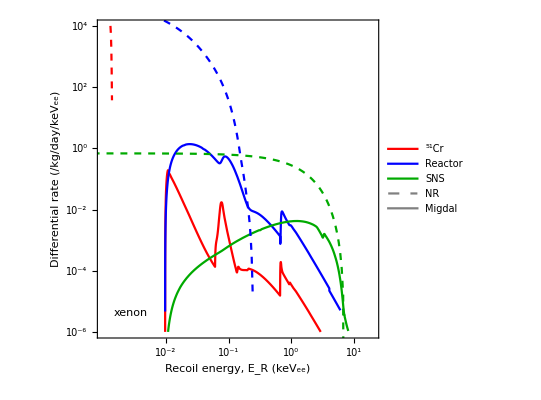
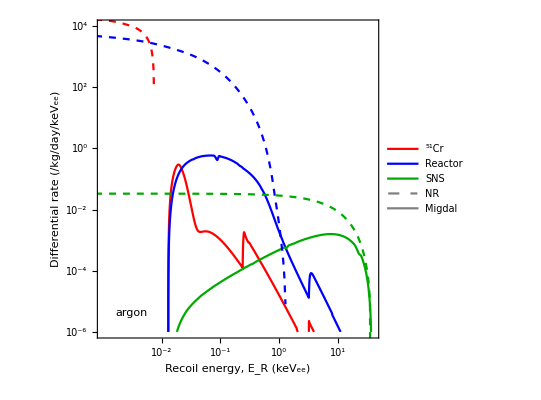

```mathematica
{XEratePlot=Show[LogLogPlot[{XEmigRateCr[er],XEmigRateReactor[er],XEmigRateSNS[er]},{er,.001,10},
PlotStyle->{Red,Blue,Green//Darker},ImageSize->400,
PlotRange->{{.001,20},{10^-6,10^4}},
PlotLegends->Legend[{"^51Cr","Reactor","SNS"},Position->{.88,.75}],
FrameLabel->{"Recoil energy, E_R (keV_ee)","Differential rate (/kg/day/keV_ee)"},
FrameTicks->{LogTicks[10^-6,10^4],LogTicks[.01,10^2]},PlotPoints->100,
Epilog->Style[Text["xenon",Scaled[{.12,.08}]],18,FontFamily->"Times"]],
ListLogLogPlot[{{0,0},{0,0},XEcrRateEdetDat,XEreactorRateEdetDat,XEsnsRateEdetDat},Joined->True,
PlotStyle->{{Dashed,Gray},Gray,{Dashed,Red},{Dashed,Blue},{Dashed,Green//Darker}},
PlotLegends->Legend[{"NR","Migdal"},Position->{.85,.9}]]],
ARratePlot=Show[LogLogPlot[{ARmigRateCr[er],ARmigRateReactor[er],ARmigRateSNS[er]},{er,.001,40},
PlotStyle->{Red,Blue,Green//Darker},ImageSize->400,
PlotRange->{{.001,40},{10^-6,10^4}},
PlotLegends->Legend[{"^51Cr","Reactor","SNS"},Position->{.88,.75}],
FrameLabel->{"Recoil energy, E_R (keV_ee)","Differential rate (/kg/day/keV_ee)"},
FrameTicks->{LogTicks[10^-6,10^4],LogTicks[.01,10^2]},PlotPoints->100,
Epilog->Style[Text["argon",Scaled[{.12,.08}]],18,FontFamily->"Times"]],
ListLogLogPlot[{{0,0},{0,0},ARcrRateEdetDat,ARreactorRateEdetDat,ARsnsRateEdetDat},Joined->True,
PlotStyle->{{Dashed,Gray},Gray,{Dashed,Red},{Dashed,Blue},{Dashed,Green//Darker}},
PlotLegends->Legend[{"NR","Migdal"},Position->{.85,.9}]]]}
```

```mathematica
Export["figures/fig_ar_nu_rates.pdf",ARratePlot];
Export["figures/fig_xe_nu_rates.pdf",XEratePlot];
```

### Integrated rates

#### Calculation

Integrate including all shells:

Xenon:

```mathematica
XEmigIntR=ParallelTable[{erMin,NIntegrate[XEmigRateReactor[er],{er,erMin,8},PrecisionGoal->3]}
,{erMin,logSpace[XEdataEM5r[[1,1]],8,100]}];
```

```mathematica
XEmigIntS=ParallelTable[{erMin,NIntegrate[XEmigRateSNS[er],{er,erMin,10},PrecisionGoal->3]}
,{erMin,logSpace[XEdataEM5s[[1,1]],8,100]}];
```

```mathematica
XEmigIntC=ParallelTable[{erMin,NIntegrate[XEmigRateCr[er],{er,erMin,5},PrecisionGoal->3]}
,{erMin,logSpace[XEdataEM5c[[1,1]],6,100]}];
```

Argon:

```mathematica
ARmigIntR=ParallelTable[{erMin,NIntegrate[ARmigRateReactor[er],{er,erMin,8},PrecisionGoal->3]}
,{erMin,logSpace[ARdataEM3r[[1,1]],8,100]}];
```

```mathematica
ARmigIntS=ParallelTable[{erMin,NIntegrate[ARmigRateSNS[er],{er,erMin,30},PrecisionGoal->3]}
,{erMin,logSpace[ARdataEM3s[[1,1]],40,100]}];
```

```mathematica
ARmigIntC=ParallelTable[{erMin,NIntegrate[ARmigRateCr[er],{er,erMin,6},PrecisionGoal->3]}
,{erMin,logSpace[ARdataEM3c[[1,1]],6,100]}];
```

Can ‘extrapolate’ to low energy (since no migdal events below ~.01eV):

```mathematica
XEmigIntR=Prepend[XEmigIntR,{10^-3,XEmigIntR[[1,2]]}];
XEmigIntS=Prepend[XEmigIntS,{10^-3,XEmigIntS[[1,2]]}];
XEmigIntC=Prepend[XEmigIntC,{10^-3,XEmigIntC[[1,2]]}];
ARmigIntR=Prepend[ARmigIntR,{10^-3,ARmigIntR[[1,2]]}];
ARmigIntS=Prepend[ARmigIntS,{10^-3,ARmigIntS[[1,2]]}];
ARmigIntC=Prepend[ARmigIntC,{10^-3,ARmigIntC[[1,2]]}];
```

#### Plots

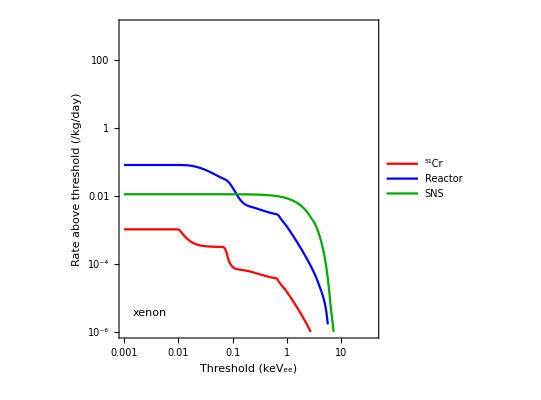
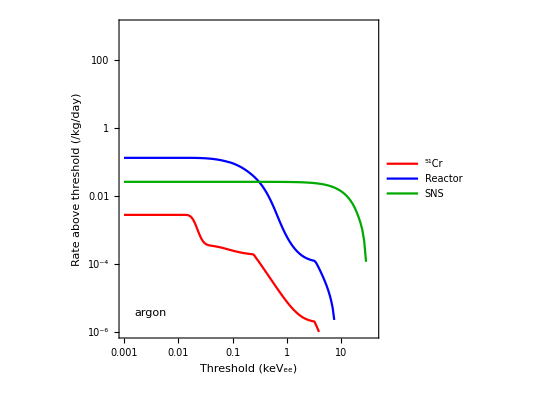

```mathematica
{XEmigIntPlot=ListLogLogPlot[{XEmigIntC,XEmigIntR,XEmigIntS},Joined->True,
PlotStyle->{Red,Blue,Green//Darker},ImageSize->400,
PlotRange->{{.001,40},{10^-6,10^3}},
PlotLegends->Legend[{"^51Cr","Reactor","SNS"},Position->{.8505,.73}],
FrameLabel->{"Threshold (keV_ee)","Rate above threshold (/kg/day)"},
FrameTicks->{LogTicks[10^-6,10^3],LogTicks[.01,10^2]},
Prolog->Inset[Framed[" ",FrameMargins->{{40,40},{50,50}},RoundingRadius->5,Background->White],Scaled[{.845,.80}]],
Epilog->Inset[Framed[Style["xenon",18,FontFamily->"Times"],RoundingRadius->5,Background->White],Scaled[{.12,.08}]]],
ARmigIntPlot=ListLogLogPlot[{ARmigIntC,ARmigIntR,ARmigIntS},Joined->True,
PlotStyle->{Red,Blue,Green//Darker},ImageSize->400,
PlotRange->{{.001,40},{10^-6,10^3}},
PlotLegends->Legend[{"^51Cr","Reactor","SNS"},Position->{.8505,.73}],
FrameLabel->{"Threshold (keV_ee)","Rate above threshold (/kg/day)"},
FrameTicks->{LogTicks[10^-6,10^3],LogTicks[.01,10^2]},
Prolog->Inset[Framed[" ",FrameMargins->{{40,40},{50,50}},RoundingRadius->5,Background->White],Scaled[{.845,.80}]],
Epilog->Inset[Framed[Style["argon",18,FontFamily->"Times"],RoundingRadius->5,Background->White],Scaled[{.12,.08}]]]}
```

#### Compare with nuclear

```mathematica
XEreactorRateIntDatEE=XEreactorRateIntDat;
XEreactorRateIntDatEE[[All,1]]*=LXe;
XEsnsRateIntDatEE=XEsnsRateIntDat;
XEsnsRateIntDatEE[[All,1]]*=LXe;
XEcrRateIntDatEE=XEcrRateIntDat;
XEcrRateIntDatEE[[All,1]]*=LXe;
```

```mathematica
ARreactorRateIntDatEE=ARreactorRateIntDat;
ARreactorRateIntDatEE[[All,1]]*=LAr;
ARsnsRateIntDatEE=ARsnsRateIntDat;
ARsnsRateIntDatEE[[All,1]]*=LAr;
ARcrRateIntDatEE=ARcrRateIntDat;
ARcrRateIntDatEE[[All,1]]*=LAr;
```

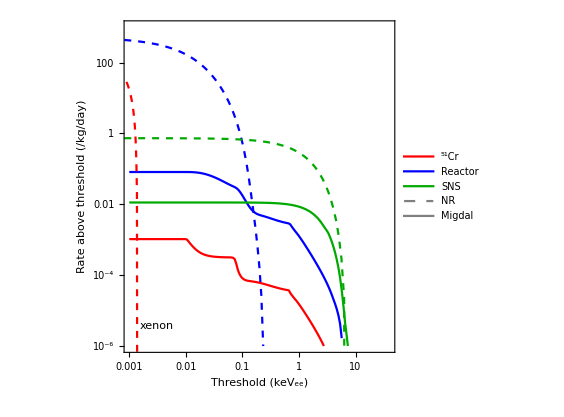
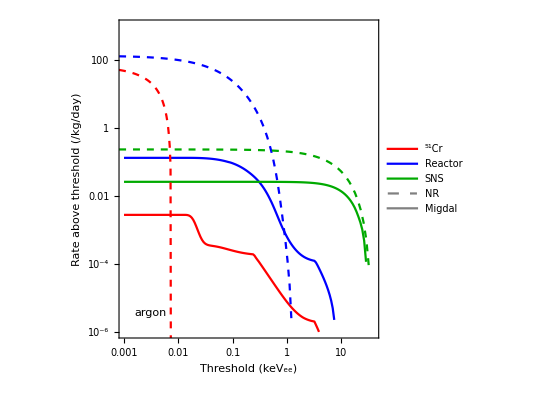

```mathematica
{XEintRatePlot=Show[XEmigIntPlot,
ListLogLogPlot[{{0,0},{0,0},XEcrRateIntDatEE,XEreactorRateIntDatEE,XEsnsRateIntDatEE},Joined->True,
PlotStyle->{{Dashed,Gray},Gray,{Dashed,Red},{Dashed,Blue},{Dashed,Green//Darker}},
PlotLegends->Legend[{"NR","Migdal"},LegendMarkerSize->{20,10},Position->{.85,.9}]]],
ARintRatePlot=Show[ARmigIntPlot,
ListLogLogPlot[{{0,0},{0,0},ARcrRateIntDatEE,ARreactorRateIntDatEE,ARsnsRateIntDatEE},Joined->True,
PlotStyle->{{Dashed,Gray},Gray,{Dashed,Red},{Dashed,Blue},{Dashed,Green//Darker}},
Prolog->Inset[Framed[" ",FrameMargins->{{32,30},{40,40}},RoundingRadius->5,Background->White],Scaled[{.82,.81}]],
PlotLegends->Legend[{"NR","Migdal"},LegendMarkerSize->{20,10},Position->{.85,.9}]]]}
```

```mathematica
Export["figures/fig_ar_nu_intRates.pdf",ARintRatePlot];
Export["figures/fig_xe_nu_intRates.pdf",XEintRatePlot];
```

Rate ratios:

```mathematica
xeReactorMigRatio=XEmigIntR[[1,2]]/XEreactorRateIntDat[[1,2]]//ScientificForm[#,2]&
```

1.7×10^-4

```mathematica
xeSNSmigRatio=XEmigIntS[[1,2]]/XEsnsRateIntDat[[1,2]]//ScientificForm[#,2]&
```

1.5×10^-2

```mathematica
xeCrMigRatio=XEmigIntC[[1,2]]/XEcrRateIntDat[[1,2]]//ScientificForm[#,2]&
```

5.4×10^-6

### Total rate comparison

Define rates as function of neutrino energy

Nuclear recoil:

```mathematica
RateNRxe[ErMin_?NumericQ,Enu_?NumericQ,flux_?NumericQ]:=flux 1/MtXe NIntegrate[UnitStep[Enu-EnuMin[Er,isotopesXe⟦1,3⟧ amu,0]]
  dσdEr[Er,Enu,isotopesXe[[4]]],
{Er,Min[ErMin,ErMax[isotopesXe⟦1,3⟧amu,Enu,0]],ErMax[isotopesXe⟦1,3⟧amu,Enu,0]},
PrecisionGoal->3]
```

```mathematica
RateNRar[ErMin_?NumericQ,Enu_?NumericQ,flux_?NumericQ]:=flux 1/MtAr NIntegrate[UnitStep[Enu-EnuMin[Er,isotopesAr⟦1,3⟧ amu,0]]
  dσdEr[Er,Enu,isotopesAr[[1]]],
{Er,Min[ErMin,ErMax[isotopesAr⟦1,3⟧amu,Enu,0]],ErMax[isotopesAr⟦1,3⟧amu,Enu,0]},
PrecisionGoal->3]
```

Migdal:

```mathematica
RateMigXe[EdetMin_?NumericQ,Enu_?NumericQ,flux_?NumericQ]:= 1/MtXe NIntegrate[
flux UnitStep[Enu-EnuMin[Er,isotopesXe⟦1,3⟧ amu,Edet-Er LXe]]dσdEr[Er,Enu,isotopesXe[[4]]]*
 Sum[
UnitStep[Edet-Er LXe -EstatesXe[[nl]]]*
ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],qe[Er,131 amu],Edet-Er LXe -EstatesXe[[nl]]],
{nl,statesXe//Length}],
{Edet,EdetMin,10keV},
{Er,ErMin[128amu,0],Min[ErMax[128amu,Enu,0],Edet/LXe]},PrecisionGoal->3,AccuracyGoal->24]
```

```mathematica
RateMigAr[EdetMin_?NumericQ,Enu_?NumericQ,flux_?NumericQ]:= flux/MtAr NIntegrate[
UnitStep[Enu-EnuMin[Er,isotopesAr⟦1,3⟧ amu,Edet-Er LXe]] dσdEr[Er,Enu,isotopesAr[[1]]]*
  Sum[
UnitStep[Edet-Er LAr -EstatesAr[[nl]]]*
ZnlAr[statesAr[[nl,1]],statesAr[[nl,2]],qe[Er,40 amu],Edet-Er LAr -EstatesAr[[nl]]],
{nl,statesAr//Length}],
{Edet,EdetMin,10keV},
{Er,ErMin[40amu,0],Min[ErMax[40amu,Enu,0],Edet/LAr]},PrecisionGoal->3,AccuracyGoal->24]
```

#### Calculations

```mathematica
XEtot0=ParallelTable[{ENU/MeV,RateNRxe[0,ENU,1]/RateNRxe[0,100MeV,1]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
XEtot1=ParallelTable[{ENU/MeV,RateNRxe[1keV,ENU,1]/RateNRxe[0,100MeV,1]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
XEtot5=ParallelTable[{ENU/MeV,RateNRxe[5keV,ENU,1]/RateNRxe[0,100MeV,1]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
```

```mathematica
ARtot0=ParallelTable[{ENU/MeV,RateNRar[0,ENU,1]/RateNRxe[0,100MeV,1]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
ARtot1=ParallelTable[{ENU/MeV,RateNRar[10keV,ENU,1]/RateNRxe[0,100MeV,1]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
ARtot5=ParallelTable[{ENU/MeV,RateNRar[20keV,ENU,1]/RateNRxe[0,100MeV,1]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
```

```mathematica
XEtotMig0=ParallelTable[{ENU/MeV,RateMigXe[10eV,ENU,1]/RateNRxe[0,100MeV,1]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
XEtotMig1=ParallelTable[{ENU/MeV,RateMigXe[1keV LXe,ENU,1]/RateNRxe[0,100MeV,1]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
XEtotMig5=ParallelTable[{ENU/MeV,RateMigXe[5keV LXe,ENU,1]/RateNRxe[0,100MeV,1]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

$Aborted

$Aborted

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.47555×10^-13 and 1.54365×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.76514×10^-13 and 8.18187×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.57833×10^-13 and 1.02699×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.94586×10^-12 and 3.31973×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.17008×10^-12 and 1.27694×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.43402×10^-13 and 2.61641×10^-16 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.25186×10^-12 and 3.72167×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.54222×10^-12 and 4.31634×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.10617×10^-13 and 3.28879×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.94902×10^-12 and 3.13191×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.25928×10^-12 and 3.81282×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.53016×10^-12 and 3.99792×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.29633×10^-12 and 2.39354×10^-15 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.62503×10^-12 and 2.83734×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
ARtotMig0=ParallelTable[{ENU/MeV,RateMigAr[10eV,ENU,1]/RateNRxe[0,100MeV,1]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
ARtotMig1=ParallelTable[{ENU/MeV,RateMigAr[10keV LAr,ENU,1]/RateNRxe[0,100MeV,1]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
ARtotMig5=ParallelTable[{ENU/MeV,RateMigAr[20keV LAr,ENU,1]/RateNRxe[0,100MeV,1]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

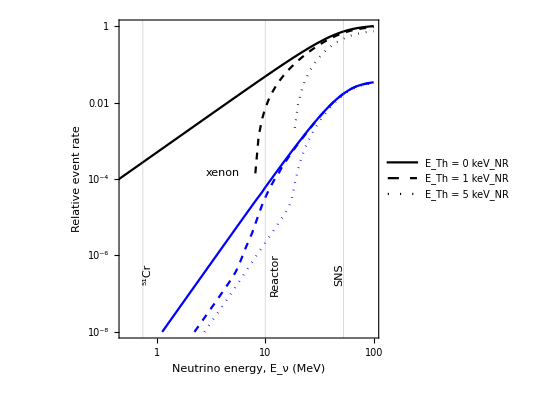
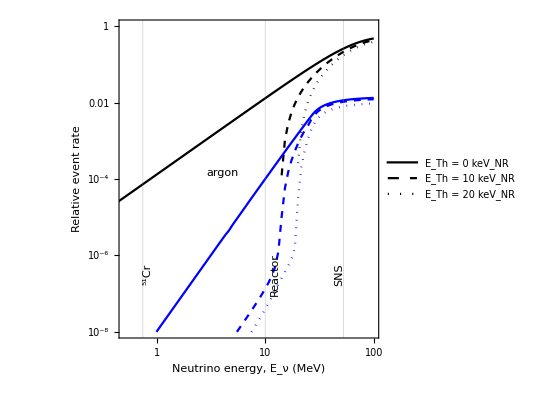

```mathematica
{nuMigPlot=ListLogLogPlot[{XEtot0,XEtot1,XEtot5,XEtotMig0,XEtotMig1,XEtotMig5},Joined->True,
PlotRange->{{.5,10^2},{10^-8, 10^0}},ImageSize->400,
FrameTicks->{LogTicks[10^-8,10^0,2],LogTicks[10^0,10^10]},
FrameLabel->{"Neutrino energy, E_ν (MeV)","Relative event rate"},
PlotLegends->Legend[{"E_Th = 0 keV_NR","E_Th = 1 keV_NR","E_Th = 5 keV_NR"},Position->{.28,.87}],
PlotStyle->{Black,{Black,Dashed},{Black,Dotted},Blue,{Blue,Dashed},{Blue,Dotted}},
GridLines->{{EνCr[[1]]/MeV,eMaxR/MeV,eMaxSNS/MeV},None},
Epilog->{Style[Text["xenon",Scaled[{.4,.52}]],16,FontFamily->"Times"],
Style[Text["^51Cr",Scaled[{.11,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],Style[Text["Reactor",Scaled[{.6,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],
Style[Text["SNS",Scaled[{.85,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5]}]
,nuMigPlotAr=ListLogLogPlot[{ARtot0,ARtot1,ARtot5,ARtotMig0,ARtotMig1,ARtotMig5},Joined->True,
PlotRange->{{.5,10^2},{10^-8, 10^0}},ImageSize->400,
FrameTicks->{LogTicks[10^-8,10^0,2],LogTicks[10^0,10^10]},
FrameLabel->{"Neutrino energy, E_ν (MeV)","Relative event rate"},
PlotLegends->Legend[{"E_Th = 0 keV_NR","E_Th = 10 keV_NR","E_Th = 20 keV_NR"},Position->{.28,.87}],
PlotStyle->{Black,{Black,Dashed},{Black,Dotted},Blue,{Blue,Dashed},{Blue,Dotted}},
GridLines->{{EνCr[[1]]/MeV,eMaxR/MeV,eMaxSNS/MeV},None},
Epilog->{Style[Text["argon",Scaled[{.4,.52}]],16,FontFamily->"Times"],
Style[Text["^51Cr",Scaled[{.11,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],
Style[Text["Reactor",Scaled[{.6,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],Style[Text["SNS",Scaled[{.85,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5]}]}
```

Comparison flux:

```mathematica
compFlux=10^10/cm2s;
```

```mathematica
XEtot0=ParallelTable[{ENU/MeV,RateNRxe[0,ENU,compFlux]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
XEtot1=ParallelTable[{ENU/MeV,RateNRxe[1keV,ENU,compFlux]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
XEtot5=ParallelTable[{ENU/MeV,RateNRxe[5keV,ENU,compFlux]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
```

```mathematica
ARtot0=ParallelTable[{ENU/MeV,RateNRar[0,ENU,compFlux]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
ARtot1=ParallelTable[{ENU/MeV,RateNRar[10keV,ENU,compFlux]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
ARtot5=ParallelTable[{ENU/MeV,RateNRar[20keV,ENU,compFlux]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
```

```mathematica
XEtotMig0=ParallelTable[{ENU/MeV,RateMigXe[10eV,ENU,compFlux]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
XEtotMig1=ParallelTable[{ENU/MeV,RateMigXe[1keV LXe,ENU,compFlux]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
XEtotMig5=ParallelTable[{ENU/MeV,RateMigXe[5keV LXe,ENU,compFlux]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
```

```mathematica
ARtotMig0=ParallelTable[{ENU/MeV,RateMigAr[10eV,ENU,compFlux]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
ARtotMig1=ParallelTable[{ENU/MeV,RateMigAr[10keV LAr,ENU,compFlux]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
ARtotMig5=ParallelTable[{ENU/MeV,RateMigAr[20keV LAr,ENU,compFlux]},{ENU,logSpace[10^-1 MeV,100MeV,100]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

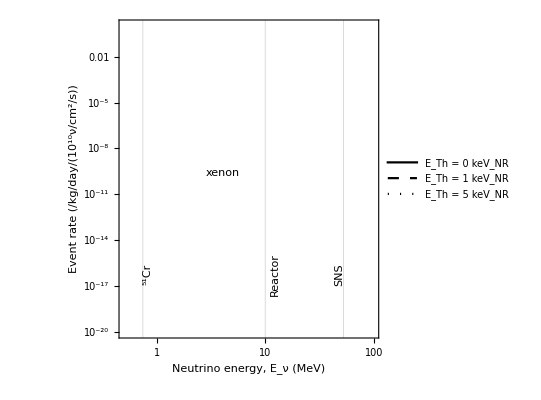
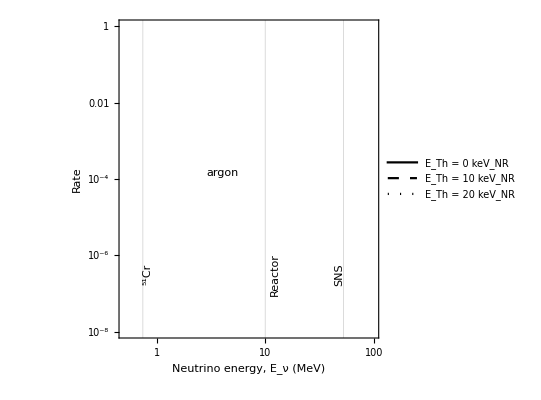

```mathematica
{nuMigPlot=ListLogLogPlot[{XEtot0,XEtot1,XEtot5,XEtotMig0,XEtotMig1,XEtotMig5},Joined->True,
PlotRange->{{.5,10^2},{10^-20, 10^0}},ImageSize->400,
FrameTicks->{LogTicks[10^-8,10^0,2],LogTicks[10^0,10^10]},
FrameLabel->{"Neutrino energy, E_ν (MeV)","Event rate (/kg/day/(10^10ν/cm^2/s))"},
PlotLegends->Legend[{"E_Th = 0 keV_NR","E_Th = 1 keV_NR","E_Th = 5 keV_NR"},Position->{.28,.87}],
PlotStyle->{Black,{Black,Dashed},{Black,Dotted},Blue,{Blue,Dashed},{Blue,Dotted}},
GridLines->{{EνCr[[1]]/MeV,eMaxR/MeV,eMaxSNS/MeV},None},
Epilog->{Style[Text["xenon",Scaled[{.4,.52}]],16,FontFamily->"Times"],
Style[Text["^51Cr",Scaled[{.11,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],Style[Text["Reactor",Scaled[{.6,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],
Style[Text["SNS",Scaled[{.85,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5]}]
,nuMigPlotAr=ListLogLogPlot[{ARtot0,ARtot1,ARtot5,ARtotMig0,ARtotMig1,ARtotMig5},Joined->True,
PlotRange->{{.5,10^2},{10^-8, 10^0}},ImageSize->400,
FrameTicks->{LogTicks[10^-8,10^0,2],LogTicks[10^0,10^10]},
FrameLabel->{"Neutrino energy, E_ν (MeV)","Rate"},
PlotLegends->Legend[{"E_Th = 0 keV_NR","E_Th = 10 keV_NR","E_Th = 20 keV_NR"},Position->{.28,.87}],
PlotStyle->{Black,{Black,Dashed},{Black,Dotted},Blue,{Blue,Dashed},{Blue,Dotted}},
GridLines->{{EνCr[[1]]/MeV,eMaxR/MeV,eMaxSNS/MeV},None},
Epilog->{Style[Text["argon",Scaled[{.4,.52}]],16,FontFamily->"Times"],
Style[Text["^51Cr",Scaled[{.11,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],
Style[Text["Reactor",Scaled[{.6,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],Style[Text["SNS",Scaled[{.85,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5]}]}
```

```mathematica
Export["figures/fig_nuErateComp.pdf",nuMigPlot];
```

```mathematica
ratioXe0={XEtot0[[All,1]],XEtotMig0[[All,2]]/XEtot0[[All,2]]}//Thread;
ratioXe1={XEtot1[[All,1]],XEtotMig1[[All,2]]/XEtot1[[All,2]]}//Thread;
ratioXe5={XEtot5[[All,1]],XEtotMig5[[All,2]]/XEtot5[[All,2]]}//Thread;
ratioAr0={ARtot0[[All,1]],ARtotMig0[[All,2]]/ARtot0[[All,2]]}//Thread;
ratioAr1={ARtot1[[All,1]],ARtotMig1[[All,2]]/ARtot1[[All,2]]}//Thread;
ratioAr5={ARtot5[[All,1]],ARtotMig5[[All,2]]/ARtot5[[All,2]]}//Thread;
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

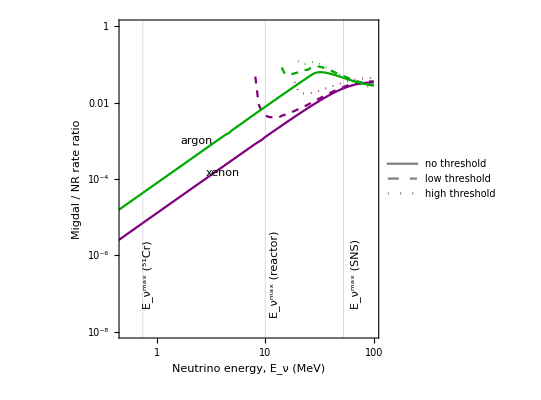

```mathematica
migdalCompPlot=ListLogLogPlot[{{{0,0}},{{0,0}},{{0,0}},ratioXe0,ratioXe1,ratioXe5,ratioAr0,ratioAr1,ratioAr5},Joined->True,
PlotRange->{{.5,10^2},{10^-8, 10^0}},ImageSize->400,
FrameTicks->{LogTicks[10^-8,10^0,2],LogTicks[10^0,10^10]},
FrameLabel->{"Neutrino energy, E_ν (MeV)","Migdal / NR rate ratio"},
PlotLegends->Legend[{"no threshold","low threshold","high threshold"},Position->{.29,.87}],
PlotStyle->{Gray,{Gray,Dashed},{Gray,Dotted},Purple,{Purple,Dashed},{Purple,Dotted},Green//Darker,{Green//Darker,Dashed},{Green//Darker,Dotted}},
GridLines->{{EνCr[[1]]/MeV,eMaxR/MeV,eMaxSNS/MeV},None},
Epilog->{Style[Text["E_ν^max (^51Cr)",Scaled[{.11,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],
Style[Text["E_ν^max (reactor)",Scaled[{.6,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],
Style[Text["E_ν^max (SNS)",Scaled[{.91,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],
Style[Text["xenon",Scaled[{.4,.52}],Automatic,{1.,.58}],16,FontFamily->"Times",Purple],
Style[Text["argon",Scaled[{.3,.62}],Automatic,{1.,.55}],16,FontFamily->"Times",Green//Darker]}]
```

```mathematica
Export["figures/fig_nuMigRatio.pdf",migdalCompPlot];
```

## S1S2 distribution

### Define plot function

```mathematica
CredibleGridPlot2D//Clear;
CredibleGridPlot2D[data_, range_,opt:OptionsPattern[{CredibleLevel -> {0.6827,0.9545}, LoggedData->{False,False}, FrameTicks->False, Smoothing->False, MaxPoint->False, SimPoint->{∞,∞}, ShowDensity->False, CredibleColor->Blue, ListContourPlot}]] := 
Module[{binData,cl, p, minx, miny, maxx, maxy, xbin, ybin, xNbins, yNbins, ft, ftX, ftY, contourPlot, densityPlot, dr, pr, prX, prY, maxPoint, maxPointCross, contSty}, 
	binData=data/Plus@@Flatten[data];
	If[Dimensions[binData]≠2,Return["List data does not have suitable dimensions"];];
	xNbins = Length[binData];
  yNbins=Length[binData[[1]]];

  minx = range[[1,1]]; 
	maxx =range[[1,2]]; 
	miny = range[[2,1]]; 
	maxy = range[[2,2]]; 
	xbin = (maxx - minx)/xNbins; 
	ybin = (maxy - miny)/yNbins; 

	(*binData = ((BinLists[ data, {minx, maxx, xbin}, {miny, maxy, ybin}, {0, 1, 1}][[All, All, 1]] // Apply[Plus, #, {2}] & ) /. 0 -> {0, 0, 0})[[All, All, 3]]//Transpose;*)

	If[OptionValue[Smoothing]==True, 
	    binData = (ArrayPad[#1, 1, 0] & )[ImageData[(GaussianFilter[#1, {2, 2}] & )[Image[binData]]]];
	    dr = {{minx - (3*xbin)/2, maxx + (3*xbin)/2}, {miny - (3*ybin)/2, maxy + (3*ybin)/2}};
	    ,
              dr = {{minx, maxx}, {miny, maxy}};
	  ];
    
    pr=FilterRules[{opt}, PlotRange];   

    If[pr == {},
        pr = {{minx,maxx},{miny,maxy},All};
        ,
        If[Length[pr[[1,2]]]==0,
         pr = {{minx,maxx},{miny,maxy},All};
        ];
        If[Depth[pr[[1,2]]]==2,
         pr=Join[{{minx,maxx}},{pr[[1,2]]},{All}]
        ];
        If[Length[pr[[1,2]]]==3,
         pr=pr[[1,2]];
        ,
            If[Length[pr[[1,2]]]==2,
             pr=Join[pr[[1,2]],{All}]
            ];
        ];
        
      ];
      
   ft = OptionValue[FrameTicks];
   If[ ft==False,
      If[OptionValue[LoggedData][[1]]==True,
	     ftX = LogTicksCP[minx,maxx];
	    ,
	     ftX = Automatic; 
	  ];
	  If[OptionValue[LoggedData][[2]]==True,
	     ftY = LogTicksCP[miny,maxy];
	    ,
	     ftY = Automatic; 
	  ];
	  ft = {ftY,ftX};
	];

    If[Length[OptionValue[CredibleLevel]]>1,
	cl = ( p /. (FindRoot[Plus @@ Plus @@ (binData*UnitStep[binData - p]) == #, {p, 0, 1}] &) /@ OptionValue[CredibleLevel])//Quiet;
    contSty={{OptionValue[CredibleColor], Dashed, Thick}, {OptionValue[CredibleColor], Thick}};
    ,
    cl = {p /. (FindRoot[Plus @@ Plus @@ (binData*UnitStep[binData - p]) == OptionValue[CredibleLevel], {p, 0, 1}] ) //Quiet};
    contSty={{OptionValue[CredibleColor], Thick}};
    ];

If[ OptionValue[ShowDensity] == True,

	contourPlot = ListContourPlot[binData, ClippingStyle -> None, PlotRange->pr, Contours -> cl, DataRange -> dr,  InterpolationOrder -> 2, ContourStyle -> {{OptionValue[CredibleColor], Dashed, Thick}, {OptionValue[CredibleColor], Thick}}, ContourShading -> None, AspectRatio->1, FrameTicks->ft, FrameStyle->Directive[Black,18,Thickness[.004]],BaseStyle->{FontFamily->"Times"}, FilterRules[ FilterRules[{opt}, Options[ListContourPlot]], Except[PlotRange]],ImageSize->400 ];

	densityPlot = ListDensityPlot[binData, PlotRange->pr, DataRange -> dr, ColorFunction -> (Opacity[#,OptionValue[CredibleColor]] &)];

	Return[Show[contourPlot,densityPlot,contourPlot]];,

	Return[ ListContourPlot[binData, Contours -> cl, PlotRange->pr, DataRange -> dr, FilterRules[ FilterRules[{opt}, Options[ListContourPlot]], Except[PlotRange]], ClippingStyle -> None, InterpolationOrder -> 2, ContourStyle -> contSty, ContourShading -> {None, Opacity[0.2, OptionValue[CredibleColor]], Opacity[0.5, OptionValue[CredibleColor]]}, FrameTicks->ft, FrameStyle->Directive[Black,18,Thickness[.004]], AspectRatio->1, BaseStyle->{FontFamily->"Times"},ImageSize->400 ] ];
	];

];
```

```mathematica
extractS1logS2[data_]:={data⟦All,2⟧,Log10[data⟦All,3⟧]}//Thread;
```

```mathematica
NotebookDirectory[]//SetDirectory;
```

### ER/NR bands

Import ER/NR bands (these are computed without cuts.

```mathematica
erDat=Import["results/S1S2_ERband_migCalHV.dat"][[5;;-2]];
```

```mathematica
nrDat=Import["results/S1S2_NRband_migCalHV.dat"][[5;;-2]];
```

Extract S1/log(S2) from simulation data

```mathematica
erS1S2dat=erDat[[5;;-2]]//extractS1logS2;
```

```mathematica
nrS1S2dat=nrDat[[5;;-2]]//extractS1logS2;
```

#### ER/NR bands in S1/logS2

```mathematica
s1binnedNR=BinLists[nrS1S2dat,{1,80,1},{0,10,10}];
```

```mathematica
s1binnedER=BinLists[erS1S2dat,{1,80,1},{0,10,10}];
```

create bands:

```mathematica
s1nrMedian={Median/@s1binnedNR[[All,1,All,1]],Median/@s1binnedNR[[All,1,All,2]]}//Thread;
s1nrDown={Median/@s1binnedNR[[All,1,All,1]],Quantile[#,.05]&/@s1binnedNR[[All,1,All,2]]}//Thread;
s1nrUp={Median/@s1binnedNR[[All,1,All,1]],Quantile[#,.95]&/@s1binnedNR[[All,1,All,2]]}//Thread;
```

```mathematica
s1erMedian={Median/@s1binnedER[[All,1,All,1]],Median/@s1binnedER[[All,1,All,2]]}//Thread;
s1erDown={Median/@s1binnedER[[All,1,All,1]],Quantile[#,.05]&/@s1binnedER[[All,1,All,2]]}//Thread;
s1erUp={Median/@s1binnedER[[All,1,All,1]],Quantile[#,.95]&/@s1binnedER[[All,1,All,2]]}//Thread;
```

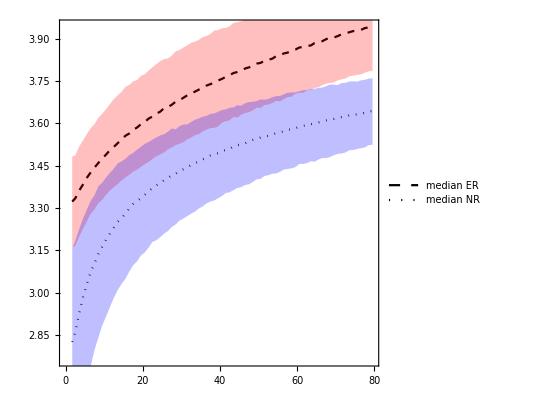

```mathematica
medians=ListPlot[{s1erMedian,s1nrMedian},Joined->True,
PlotStyle->{{Black,Dashed},{Black,Dotted}},PlotLegends->Legend[{"median ER","median NR"},Position->{.8,.15},LegendMarkerSize->{20,10}]];
bands=Show[ListPlot[{s1erDown,s1erUp},Filling->1->{2},Joined->True,FillingStyle->Opacity[.25,Red],PlotStyle->None],
ListPlot[{s1nrDown,s1nrUp},Filling->1->{2},Joined->True,FillingStyle->Opacity[.25,Blue],PlotStyle->None]];
Show[medians,bands]
```

#### Estimate efficiency curve before cuts

```mathematica
binnedNR=BinCounts[nrDat[[All,-2]],{0,Max[nrDat[[6;;-2,-2]]],.4}];
binnedER=BinCounts[erDat[[All,-2]],{0,Max[erDat[[6;;-2,-2]]],.1}];
```

```mathematica
effNRxe={Table[.2+ii,{ii,0,Max[nrDat[[6;;-2,-2]]]-.4,.4}],binnedNR/Mean[binnedNR[[50;;100]]]}//Thread//Interpolation//N;
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
effERxe={Table[.05+ii,{ii,0,Max[erDat[[6;;-2,-2]]]-.1,.1}],binnedER/Mean[binnedER[[40;;80]]]}//Thread//Interpolation//N
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

InterpolatingFunction[{{0.05, 20717.3}}, <>]

```mathematica
Show[Plot[effNRxe[x],{x,.2,20}],ListPlot[{Table[.2+ii,{ii,0,Max[nrDat[[6;;-2,-2]]]-.4,.4}],binnedNR/Mean[binnedNR[[50;;100]]]}//Thread]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
Show[Plot[effERxe[x],{x,.1,10},PlotRange->{0,1}],ListPlot[{Table[.05+ii,{ii,0,Max[erDat[[6;;-2,-2]]]-.1,.1}],binnedER/Mean[binnedER[[40;;80]]]}//Thread]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

### Detector simulation

#### Import

```mathematica
reactorDat=Import["results/S1S2_reactorNu_NRm_migCalHV_xe.dat"][[5;;-2]];
```

```mathematica
snsDat=Import["results/S1S2_snsNu_NRm_migCalHV_xe.dat"][[5;;-2]];
```

```mathematica
crDat=Import["results/S1S2_crNu_NRmOp_migCalHV_xe.dat"][[5;;-2]];
```

Import the effective exposure required for the simulations (used to normalize rates that pass cuts):

```mathematica
exposureR=Import["results/S1S2_reactorNu_NRm_migCalHV_xe.dat"][[-1,3]]tonne yr;
exposureS=Import["results/S1S2_snsNu_NRm_migCalHV_xe.dat"][[-1,3]]tonne yr;
ratioC=Import["results/S1S2_crNu_NRmOp_migCalHV_xe.dat"][[-1,4]];
```

Select out NR and Migdal recoils:

```mathematica
reactorMigOnlyDat=Select[reactorDat,#[[4]]>0&];
reactorNRonlyDat=Select[reactorDat,#[[4]]==0&];
```

```mathematica
snsMigOnlyDat=Select[snsDat,#[[4]]>0&];
snsNRonlyDat=Select[snsDat,#[[4]]==0&];
```

```mathematica
crMigOnlyDat=Select[crDat,#[[4]]>0&];
crNRonlyDat=Select[crDat,#[[4]]==0&];
```

#### Migdal to nuclear event ratios

```mathematica
rRatio=(reactorMigOnlyDat//Length)/(reactorNRonlyDat//Length)//Round[#,.01]&
```

0.11

```mathematica
sRatio=(snsMigOnlyDat//Length)/(snsNRonlyDat//Length)//Round[#,.01]&
```

0.02

```mathematica
(crMigOnlyDat//Length)/(crNRonlyDat//Length)
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

#### Event rates

```mathematica
nrRateR=(reactorNRonlyDat//Length)/exposureR
```

1428.57/(tonne yr)

```mathematica
migRateR=(reactorMigOnlyDat//Length)/(exposureR (365250kg days/tonne/yr))//ScientificForm[#,2]&
```

(4.3×10^-4)/(days kg)

```mathematica
nrRateS=(snsNRonlyDat//Length)/exposureS
```

165227./(tonne yr)

```mathematica
migRateS=(snsMigOnlyDat//Length)/(exposureS (365250kg days/tonne/yr))//ScientificForm[#,2]&
```

(8.8×10^-3)/(days kg)

Needs a correction because optimized rate was used which scales Migdal probability and since only Migdal events were observed we have:

```mathematica
totNuclearRateC=NIntegrate[dRcdExe[er,0](KilogramDay),{er,1eV,ErMax[128 amu/GeV,EνCr⟦1⟧,0]}]/kg /days;
migRateC=ratioC/52348 totNuclearRateC
```

(8.18155×10^-6)/(days kg)

#### Optional

Cut:

```mathematica
neutronMigDat=Select[neutronMigDat,#[[2]]≥2&];
```

```mathematica
neutronMigS1S2=neutronMigDat//extractS1logS2;
```

```mathematica
neutronMigES1S2=neutronMigDatE//extractS1logS2;
```

```mathematica
neutronMigEonlyS1S2=neutronMigDatEonly//extractS1logS2;
```

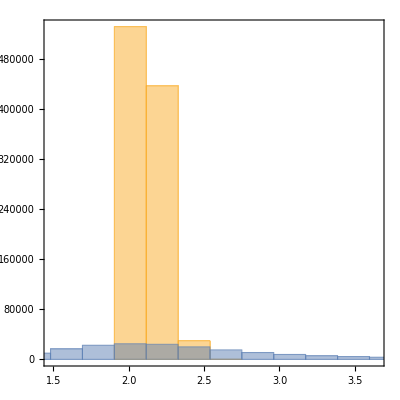

```mathematica
Histogram[{neutronS1S2dat[[All,2]],neutronMigDat[[All,2]]},Automatic]
```

#### Spectra

```mathematica
cosθi[neutronMigDat[[ii,7]] 10^-6,17 10^-6,(neutronMigDat[[ii,4]]+neutronMigDat[[ii,5]])10^-6,131.3 amu/GeV]
```

```mathematica
Do[snsMigOnlyDat[[ii]]=Join[snsMigOnlyDat[[ii]],{snsMigOnlyDat[[ii,4]]+snsMigOnlyDat[[ii,5]]+0.15snsMigOnlyDat[[ii,7]]}],{ii,1,Length[snsMigOnlyDat]}]
```

```mathematica
Do[reactorMigOnlyDat[[ii]]=Join[reactorMigOnlyDat[[ii]],{reactorMigOnlyDat[[ii,4]]+reactorMigOnlyDat[[ii,5]]+0.15reactorMigOnlyDat[[ii,7]]}],{ii,1,Length[reactorMigOnlyDat]}]
```

Number of elastic neutron scatters per observed Migdal event:

```mathematica
NRevents=Select[neutronMigDat,(#[[4]]==0&)];
```

MC true energy:

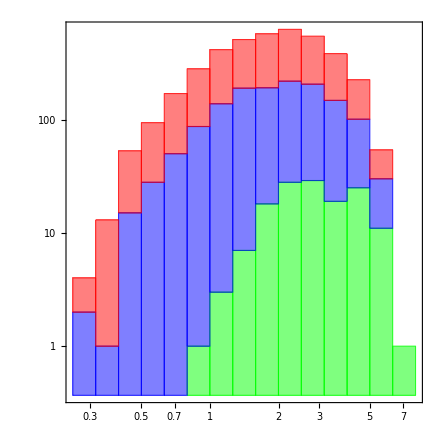

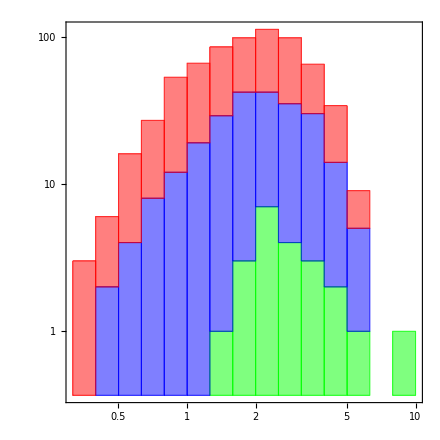

```mathematica
Histogram[{Select[snsMigOnlyDat,(#[[6]]==3&)][[All,-1]],Select[snsMigOnlyDat,(#[[6]]==4&)][[All,-1]],Select[snsMigOnlyDat,(#[[6]]==5&)][[All,-1]]},{"Log",14},{"Log","Count"},PlotRange->{{0,8},All},ChartStyle->{Green ,Blue,Red},ChartLayout->"Stacked"]
```

InterpolatingFunction::dmval: Input value {0.00100009} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

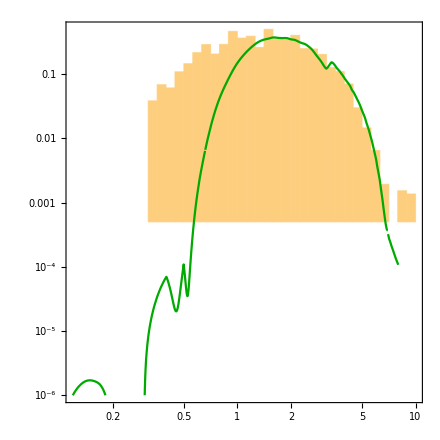

```mathematica
Show[Histogram[snsMigOnlyDat[[All,-1]],{"Log",40},{"Log","PDF"},PlotRange->{{0,8},All}],LogLogPlot[200effERxe[er]XEmigRateSNS[er],{er,.001,10},
PlotStyle->{Red,Blue,Green//Darker},ImageSize->400,
PlotRange->{{.01,20},{10^-6,10^4}},
FrameLabel->{"Recoil energy, E_R (keV_ee)","Differential rate (/kg/day/keV_ee)"},
FrameTicks->{LogTicks[10^-6,10^4],LogTicks[.01,10^2]},PlotPoints->100,
Epilog->Style[Text["xenon",Scaled[{.12,.08}]],18,FontFamily->"Times"]]]
```

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}} cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}} cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

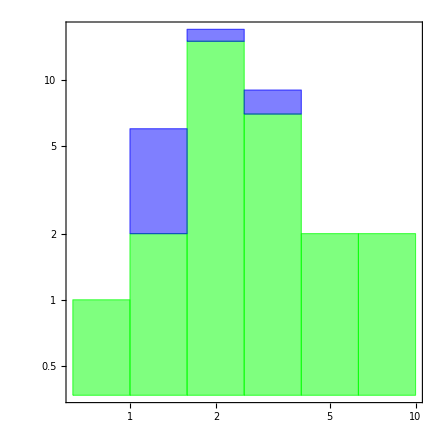

```mathematica
Histogram[{Select[reactorMigOnlyDat,(#[[6]]==3&)][[All,-1]],Select[reactorMigOnlyDat,(#[[6]]==4&)][[All,-1]],Select[reactorMigOnlyDat,(#[[6]]==5&)][[All,-1]]},"Log",{"Log","Count"},PlotRange->{{0,8},All},ChartStyle->{Green ,Blue,Red},ChartLayout->"Stacked"]
```

### Region plots

Bin the MC data:

```mathematica
NRsnsBinnedS1S2=BinCounts[snsNRonlyDat//extractS1logS2,{2,100,1},{1,4,.1}]//Transpose;
MIGsnsBinnedS1S2=BinCounts[snsMigOnlyDat//extractS1logS2,{2,100,1},{1,4,.1}]//Transpose;
```

```mathematica
NRrBinnedS1S2=BinCounts[reactorNRonlyDat//extractS1logS2,{2,100,1},{1,4.2,.1}]//Transpose;
MIGrBinnedS1S2=BinCounts[reactorMigOnlyDat//extractS1logS2,{2,100,1},{1,4.2,.1}]//Transpose;
```

```mathematica
MIGcrBinnedS1S2=BinCounts[crMigOnlyDat//extractS1logS2,{2,100,1},{1,4.2,.1}]//Transpose;
```

#### Reactor

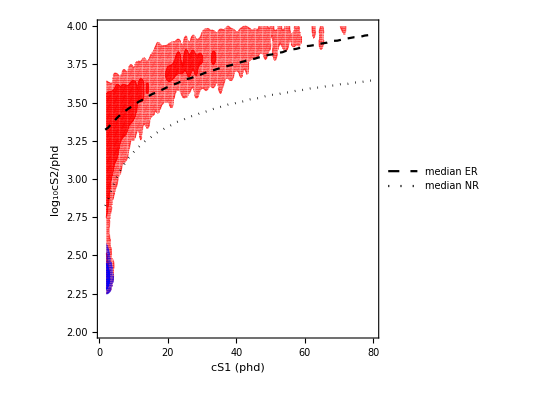

```mathematica
RmigVsNRplot=Show[CredibleGridPlot2D[MIGrBinnedS1S2,{{2,100},{1,4.2}},CredibleColor->Red,PlotRange->{{1,80},{2,4}},FrameLabel->{"cS1 (phd)","log_10cS2/phd"}],CredibleGridPlot2D[NRrBinnedS1S2,{{2,100},{1,4}}],medians]
```

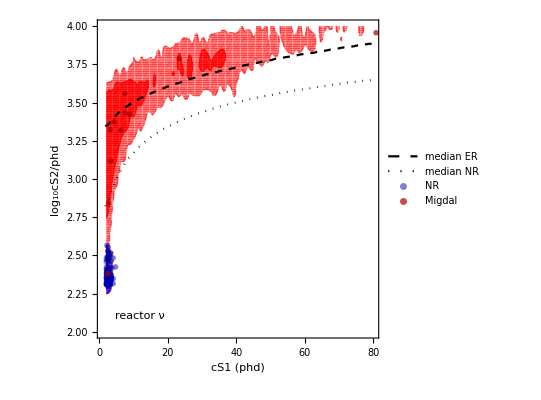

```mathematica
Rs1s2plot =Show[RmigVsNRplot,
ListPlot[{reactorNRonlyDat[[1;;107]]//extractS1logS2,reactorMigOnlyDat[[1;;11]]//extractS1logS2},
PlotStyle->{Directive[Opacity[.5,Blue//Darker],PointSize->.01],Directive[Opacity[.7,Red//Darker],PointSize->.01]},
PlotLegends->Legend[{"NR","Migdal"},Position->{.75,.4},LegendMarkerSize->20,LegendMarkers->"●"]],
Epilog->Style[Text["reactor ν",Scaled[{.15,.07}]],17,FontFamily->"Times"]]
```

Alternately import optimized events (doesn’t have correct NR:Mig ratio, but will sample the S1S2 space for the Migdal events correctly)

```mathematica
reactorDatOp=Import["results/S1S2_reactorNu_NRmOp_migCalHV_xe.dat"][[5;;-2]];
```

```mathematica
reactorMigOnlyDatOp=Select[reactorDatOp,#[[4]]>0&];
```

```mathematica
MIGrOpBinnedS1S2=BinCounts[reactorMigOnlyDatOp//extractS1logS2,{2,100,1},{1,4.2,.1}]//Transpose;
```

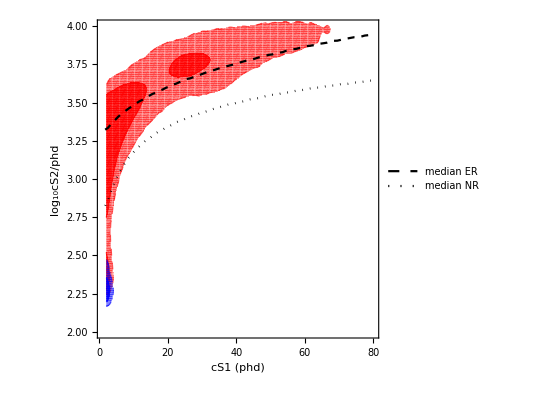

```mathematica
RmigOpVsNRplot=Show[CredibleGridPlot2D[MIGrOpBinnedS1S2,{{2,100},{1,4.2}},CredibleColor->Red,PlotRange->{{1,80},{2,4}},FrameLabel->{"cS1 (phd)","log_10cS2/phd"}],CredibleGridPlot2D[NRrBinnedS1S2,{{2,100},{1,4}}],medians]
```

Choose a representative exposure:

```mathematica
reactorExp=0.1tonne yr;
```

Calculate number of events to show:

```mathematica
NreactorNR=Round[reactorExp*nrRateR];
NreactorMig=Round[NreactorNR*rRatio];
```

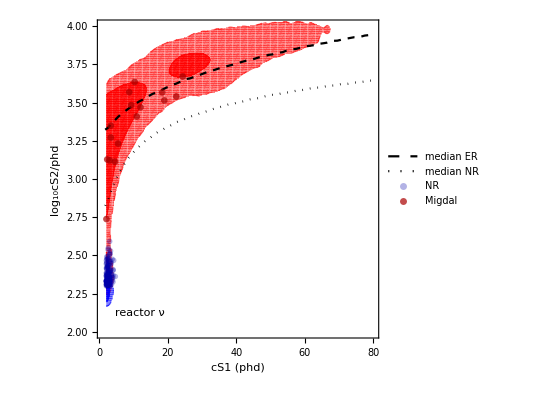

```mathematica
Rs1s2plot =Show[RmigOpVsNRplot,
ListPlot[{reactorNRonlyDat[[1;;NreactorNR]]//extractS1logS2,reactorMigOnlyDat[[1;;NreactorMig]]//extractS1logS2},
PlotStyle->{Directive[Opacity[.3,Blue//Darker],PointSize->.01],Directive[Opacity[ .7,Red//Darker],PointSize->.012]},
PlotLegends->Legend[{"NR","Migdal"},Position->{.76,.31},LegendMarkerSize->20,LegendMarkers->"●"]],
Prolog->Inset[Framed[" ",FrameMargins->{{42,55},{42,50}},RoundingRadius->5,Background->White],Scaled[{.79,.24}]],
Epilog->Inset[Framed[Style["reactor ν",17,FontFamily->"Times"],RoundingRadius->5,Background->White],Scaled[{.15,.08}]]]
```

#### SNS

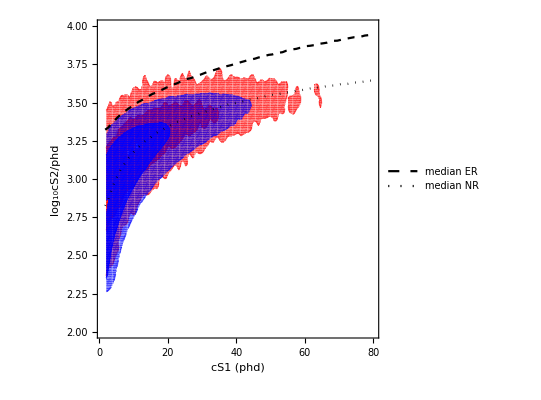

```mathematica
SNSmigVsNRplot=Show[CredibleGridPlot2D[MIGsnsBinnedS1S2,{{2,100},{1,4}},CredibleColor->Red,PlotRange->{{1,80},{2,4}},FrameLabel->{"cS1 (phd)","log_10cS2/phd"}],
CredibleGridPlot2D[NRsnsBinnedS1S2,{{2,100},{1,4}}],medians]
```

SNS optimized:

```mathematica
snsDatOp=Import["results/S1S2_snsNu_NRmOp_migCalHV_xe.dat"][[5;;-2]];
snsMigOnlyDatOp=Select[snsDatOp,#[[4]]>0&];
MIGsnsOpBinnedS1S2=BinCounts[snsMigOnlyDatOp//extractS1logS2,{2,100,1},{1,4,.1}]//Transpose;
```

```mathematica
SNSmigVsNRplot=Show[CredibleGridPlot2D[MIGsnsOpBinnedS1S2,{{2,100},{1,4}},CredibleColor->Red,PlotRange->{{1,80},{2,4}},FrameLabel->{"cS1 (phd)","log_10cS2/phd"}],
CredibleGridPlot2D[NRsnsBinnedS1S2,{{2,100},{1,4}}],medians];
```

Choose a representative exposure:

```mathematica
snsExp=0.01tonne yr;
```

Calculate number of events to show:

```mathematica
NsnsNR=Round[snsExp*nrRateS];
NsnsMig=Round[NsnsNR*sRatio];
```

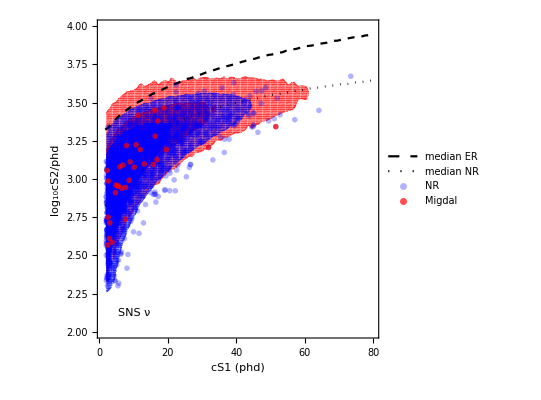

```mathematica
SNSs1s2plot=Show[SNSmigVsNRplot,
ListPlot[{snsNRonlyDat[[1;;NsnsNR]]//extractS1logS2,snsNRonlyDat[[1;;NsnsMig]]//extractS1logS2},
PlotStyle->{Directive[Opacity[.3,Blue],PointSize->.01],Directive[Opacity[.7,Red],PointSize->.01]},
PlotLegends->Legend[{"NR","Migdal"},Position->{.76,.31},LegendMarkerSize->20,LegendMarkers->"●"]],
Prolog->Inset[Framed[" ",FrameMargins->{{42,55},{42,50}},RoundingRadius->5,Background->White],Scaled[{.79,.24}]],
Epilog->Inset[Framed[Style["SNS ν",17,FontFamily->"Times"],RoundingRadius->5,Background->White],Scaled[{.13,.08}]]
]
```

#### Chromium

```mathematica
CRmigVsNRplot=Show[CredibleGridPlot2D[MIGcrBinnedS1S2,{{2,100},{1,4.2}},CredibleColor->Red,PlotRange->{{1,80},{2.2,4}},FrameLabel->{"cS1 (phd)","log_10cS2/phd"}],medians];
```

Choose a representative exposure:

```mathematica
crExp=10tonne yr;
```

Calculate number of events to show:

```mathematica
NcrMig=Round[crExp migRateC (365250 kg days)/(1 tonne yr)];
```

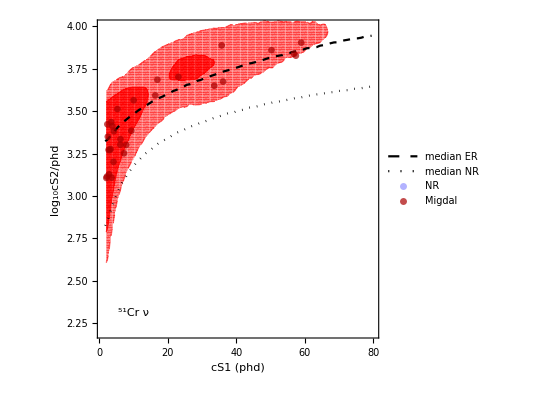

```mathematica
Cs1s2plot=Show[CRmigVsNRplot,
ListPlot[{{{0,0}},crMigOnlyDat[[1;;NcrMig]]//extractS1logS2},
PlotStyle->{Directive[Opacity[.3,Blue],PointSize->.01],Directive[Opacity[.7,Red//Darker],PointSize->.012]},
PlotLegends->Legend[{"NR","Migdal"},Position->{.76,.31},LegendMarkerSize->20,LegendMarkers->"●"]],
Prolog->Inset[Framed[" ",FrameMargins->{{42,55},{42,50}},RoundingRadius->5,Background->White],Scaled[{.79,.24}]],
Epilog->Inset[Framed[Style["^51Cr ν",17,FontFamily->"Times"],RoundingRadius->5,Background->White],Scaled[{.13,.08}]]]
```

#### Export

```mathematica
Export["figures/fig_xe_reactor_S1S2.pdf",Rasterize[Rs1s2plot,ImageResolution->500]];
Export["figures/fig_xe_sns_S1S2.pdf",Rasterize[SNSs1s2plot,ImageResolution->500]];
Export["figures/fig_xe_cr_S1S2.pdf",Rasterize[Cs1s2plot,ImageResolution->500]];
```